### Start choosing the example:

```mathematica
t=21;
beta = 1;
A =0;
g[x]
```

x

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesData.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{}|>;
d2e = Data2Equations[Data/.{I1->1,I2->2,U1->1,U2->2, U3->3}];
```

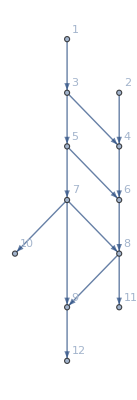
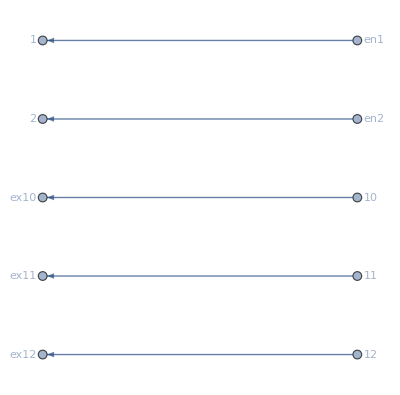
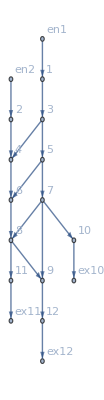
NonLinear[<|Vertices List→{1,2,3,4,5,6,7,8,9,10,11,12},Adjacency Matrix→{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,1},{2,2}},Exit Vertices and Terminal Costs→{{10,1},{11,2},{12,3}},Switching Costs→{},VL→{1,2,3,4,5,6,7,8,9,10,11,12},AM→{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},EVC→{{1,1},{2,2}},EVTC→{{10,1},{11,2},{12,3}},SC→{},BG→-Graphics-,EntranceVertices→{1,2},InwardVertices→<|1→en1,2→en2|>,ExitVertices→{10,11,12},OutwardVertices→<|10→ex10,11→ex11,12→ex12|>,InEdges→{en1->1,en2->2},OutEdges→{10->ex10,11->ex11,12->ex12},AuxiliaryGraph→-Graphics-,FG→-Graphics-,EL→{1->3,2->4,3->4,3->5,4->6,5->6,5->7,6->8,7->8,7->9,7->10,8->9,8->11,9->12,10->ex10,11->ex11,12->ex12,en1->1,en2->2},BEL→{1->3,2->4,3->4,3->5,4->6,5->6,5->7,6->8,7->8,7->9,7->10,8->9,8->11,9->12},FVL→{1,2,3,4,5,6,7,8,9,10,11,12,en1,en2,ex10,ex11,ex12},jargs→{{1,1->3},{3,1->3},{2,2->4},{4,2->4},{3,3->4},{4,3->4},{3,3->5},{5,3->5},{4,4->6},{6,4->6},{5,5->6},{6,5->6},{5,5->7},{7,5->7},{6,6->8},{8,6->8},{7,7->8},{8,7->8},{7,7->9},{9,7->9},{7,7->10},{10,7->10},{8,8->9},{9,8->9},{8,8->11},{11,8->11},{9,9->12},{12,9->12},{10,10->ex10},{ex10,10->ex10},{11,11->ex11},{ex11,11->ex11},{12,12->ex12},{ex12,12->ex12},{en1,en1->1},{1,en1->1},{en2,en2->2},{2,en2->2}},uargs→{{1,1->3},{3,1->3},{2,2->4},{4,2->4},{3,3->4},{4,3->4},{3,3->5},{5,3->5},{4,4->6},{6,4->6},{5,5->6},{6,5->6},{5,5->7},{7,5->7},{6,6->8},{8,6->8},{7,7->8},{8,7->8},{7,7->9},{9,7->9},{7,7->10},{10,7->10},{8,8->9},{9,8->9},{8,8->11},{11,8->11},{9,9->12},{12,9->12},{10,10->ex10},{ex10,10->ex10},{11,11->ex11},{ex11,11->ex11},{12,12->ex12},{ex12,12->ex12},{en1,en1->1},{1,en1->1},{en2,en2->2},{2,en2->2}},AllTransitions→{{1,1->3,en1->1},{1,en1->1,1->3},{2,2->4,en2->2},{2,en2->2,2->4},{3,1->3,3->4},{3,1->3,3->5},{3,3->4,1->3},{3,3->4,3->5},{3,3->5,1->3},{3,3->5,3->4},{4,2->4,3->4},{4,2->4,4->6},{4,3->4,2->4},{4,3->4,4->6},{4,4->6,2->4},{4,4->6,3->4},{5,3->5,5->6},{5,3->5,5->7},{5,5->6,3->5},{5,5->6,5->7},{5,5->7,3->5},{5,5->7,5->6},{6,4->6,5->6},{6,4->6,6->8},{6,5->6,4->6},{6,5->6,6->8},{6,6->8,4->6},{6,6->8,5->6},{7,5->7,7->8},{7,5->7,7->9},{7,5->7,7->10},{7,7->8,5->7},{7,7->8,7->9},{7,7->8,7->10},{7,7->9,5->7},{7,7->9,7->8},{7,7->9,7->10},{7,7->10,5->7},{7,7->10,7->8},{7,7->10,7->9},{8,6->8,7->8},{8,6->8,8->9},{8,6->8,8->11},{8,7->8,6->8},{8,7->8,8->9},{8,7->8,8->11},{8,8->9,6->8},{8,8->9,7->8},{8,8->9,8->11},{8,8->11,6->8},{8,8->11,7->8},{8,8->11,8->9},{9,7->9,8->9},{9,7->9,9->12},{9,8->9,7->9},{9,8->9,9->12},{9,9->12,7->9},{9,9->12,8->9},{10,7->10,10->ex10},{10,10->ex10,7->10},{11,8->11,11->ex11},{11,11->ex11,8->11},{12,9->12,12->ex12},{12,12->ex12,9->12}},EntryArgs→{{1,en1->1},{2,en2->2}},EntryDataAssociation→<|{1,en1->1}→1,{2,en2->2}→2|>,ExitCosts→<|ex10→1,ex11→2,ex12→3|>,js→{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j20,j21,j22,j23,j24,j25,j26,j27,j28,j29,j30,j31,j32,j33,j34,j35,j36,j37,j38},jvars→<|{1,1->3}→j1,{3,1->3}→j2,{2,2->4}→j3,{4,2->4}→j4,{3,3->4}→j5,{4,3->4}→j6,{3,3->5}→j7,{5,3->5}→j8,{4,4->6}→j9,{6,4->6}→j10,{5,5->6}→j11,{6,5->6}→j12,{5,5->7}→j13,{7,5->7}→j14,{6,6->8}→j15,{8,6->8}→j16,{7,7->8}→j17,{8,7->8}→j18,{7,7->9}→j19,{9,7->9}→j20,{7,7->10}→j21,{10,7->10}→j22,{8,8->9}→j23,{9,8->9}→j24,{8,8->11}→j25,{11,8->11}→j26,{9,9->12}→j27,{12,9->12}→j28,{10,10->ex10}→j29,{ex10,10->ex10}→j30,{11,11->ex11}→j31,{ex11,11->ex11}→j32,{12,12->ex12}→j33,{ex12,12->ex12}→j34,{en1,en1->1}→j35,{1,en1->1}→j36,{en2,en2->2}→j37,{2,en2->2}→j38|>,us→{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,u11,u12,u13,u14,u15,u16,u17,u18,u19,u20,u21,u22,u23,u24,u25,u26,u27,u28,u29,u30,u31,u32,u33,u34,u35,u36,u37,u38},uvars→<|{1,1->3}→u1,{3,1->3}→u2,{2,2->4}→u3,{4,2->4}→u4,{3,3->4}→u5,{4,3->4}→u6,{3,3->5}→u7,{5,3->5}→u8,{4,4->6}→u9,{6,4->6}→u10,{5,5->6}→u11,{6,5->6}→u12,{5,5->7}→u13,{7,5->7}→u14,{6,6->8}→u15,{8,6->8}→u16,{7,7->8}→u17,{8,7->8}→u18,{7,7->9}→u19,{9,7->9}→u20,{7,7->10}→u21,{10,7->10}→u22,{8,8->9}→u23,{9,8->9}→u24,{8,8->11}→u25,{11,8->11}→u26,{9,9->12}→u27,{12,9->12}→u28,{10,10->ex10}→u29,{ex10,10->ex10}→u30,{11,11->ex11}→u31,{ex11,11->ex11}→u32,{12,12->ex12}→u33,{ex12,12->ex12}→u34,{en1,en1->1}→u35,{1,en1->1}→u36,{en2,en2->2}→u37,{2,en2->2}→u38|>,jts→{jt1,jt2,jt3,jt4,jt5,jt6,jt7,jt8,jt9,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt60,jt61,jt62,jt63,jt64},jtvars→<|{1,1->3,en1->1}→jt1,{1,en1->1,1->3}→jt2,{2,2->4,en2->2}→jt3,{2,en2->2,2->4}→jt4,{3,1->3,3->4}→jt5,{3,1->3,3->5}→jt6,{3,3->4,1->3}→jt7,{3,3->4,3->5}→jt8,{3,3->5,1->3}→jt9,{3,3->5,3->4}→jt10,{4,2->4,3->4}→jt11,{4,2->4,4->6}→jt12,{4,3->4,2->4}→jt13,{4,3->4,4->6}→jt14,{4,4->6,2->4}→jt15,{4,4->6,3->4}→jt16,{5,3->5,5->6}→jt17,{5,3->5,5->7}→jt18,{5,5->6,3->5}→jt19,{5,5->6,5->7}→jt20,{5,5->7,3->5}→jt21,{5,5->7,5->6}→jt22,{6,4->6,5->6}→jt23,{6,4->6,6->8}→jt24,{6,5->6,4->6}→jt25,{6,5->6,6->8}→jt26,{6,6->8,4->6}→jt27,{6,6->8,5->6}→jt28,{7,5->7,7->8}→jt29,{7,5->7,7->9}→jt30,{7,5->7,7->10}→jt31,{7,7->8,5->7}→jt32,{7,7->8,7->9}→jt33,{7,7->8,7->10}→jt34,{7,7->9,5->7}→jt35,{7,7->9,7->8}→jt36,{7,7->9,7->10}→jt37,{7,7->10,5->7}→jt38,{7,7->10,7->8}→jt39,{7,7->10,7->9}→jt40,{8,6->8,7->8}→jt41,{8,6->8,8->9}→jt42,{8,6->8,8->11}→jt43,{8,7->8,6->8}→jt44,{8,7->8,8->9}→jt45,{8,7->8,8->11}→jt46,{8,8->9,6->8}→jt47,{8,8->9,7->8}→jt48,{8,8->9,8->11}→jt49,{8,8->11,6->8}→jt50,{8,8->11,7->8}→jt51,{8,8->11,8->9}→jt52,{9,7->9,8->9}→jt53,{9,7->9,9->12}→jt54,{9,8->9,7->9}→jt55,{9,8->9,9->12}→jt56,{9,9->12,7->9}→jt57,{9,9->12,8->9}→jt58,{10,7->10,10->ex10}→jt59,{10,10->ex10,7->10}→jt60,{11,8->11,11->ex11}→jt61,{11,11->ex11,8->11}→jt62,{12,9->12,12->ex12}→jt63,{12,12->ex12,9->12}→jt64|>,SignedCurrents→<|1->3→-j1+j2,2->4→-j3+j4,3->4→-j5+j6,3->5→-j7+j8,4->6→j10-j9,5->6→-j11+j12,5->7→-j13+j14,6->8→-j15+j16,7->8→-j17+j18,7->9→-j19+j20,7->10→-j21+j22,8->9→-j23+j24,8->11→-j25+j26,9->12→-j27+j28|>,SwitchingCosts→<|{1,1->3,en1->1}→0,{1,en1->1,1->3}→0,{2,2->4,en2->2}→0,{2,en2->2,2->4}→0,{3,1->3,3->4}→0,{3,1->3,3->5}→0,{3,3->4,1->3}→0,{3,3->4,3->5}→0,{3,3->5,1->3}→0,{3,3->5,3->4}→0,{4,2->4,3->4}→0,{4,2->4,4->6}→0,{4,3->4,2->4}→0,{4,3->4,4->6}→0,{4,4->6,2->4}→0,{4,4->6,3->4}→0,{5,3->5,5->6}→0,{5,3->5,5->7}→0,{5,5->6,3->5}→0,{5,5->6,5->7}→0,{5,5->7,3->5}→0,{5,5->7,5->6}→0,{6,4->6,5->6}→0,{6,4->6,6->8}→0,{6,5->6,4->6}→0,{6,5->6,6->8}→0,{6,6->8,4->6}→0,{6,6->8,5->6}→0,{7,5->7,7->8}→0,{7,5->7,7->9}→0,{7,5->7,7->10}→0,{7,7->8,5->7}→0,{7,7->8,7->9}→0,{7,7->8,7->10}→0,{7,7->9,5->7}→0,{7,7->9,7->8}→0,{7,7->9,7->10}→0,{7,7->10,5->7}→0,{7,7->10,7->8}→0,{7,7->10,7->9}→0,{8,6->8,7->8}→0,{8,6->8,8->9}→0,{8,6->8,8->11}→0,{8,7->8,6->8}→0,{8,7->8,8->9}→0,{8,7->8,8->11}→0,{8,8->9,6->8}→0,{8,8->9,7->8}→0,{8,8->9,8->11}→0,{8,8->11,6->8}→0,{8,8->11,7->8}→0,{8,8->11,8->9}→0,{9,7->9,8->9}→0,{9,7->9,9->12}→0,{9,8->9,7->9}→0,{9,8->9,9->12}→0,{9,9->12,7->9}→0,{9,9->12,8->9}→0,{10,7->10,10->ex10}→0,{10,10->ex10,7->10}→0,{11,8->11,11->ex11}→0,{11,11->ex11,8->11}→0,{12,9->12,12->ex12}→0,{12,12->ex12,9->12}→0|>,EqPosJs→j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0&&j27≥0&&j28≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j33≥0&&j34≥0&&j35≥0&&j36≥0&&j37≥0&&j38≥0,EqPosJts→jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0&&jt33≥0&&jt34≥0&&jt35≥0&&jt36≥0&&jt37≥0&&jt38≥0&&jt39≥0&&jt40≥0&&jt41≥0&&jt42≥0&&jt43≥0&&jt44≥0&&jt45≥0&&jt46≥0&&jt47≥0&&jt48≥0&&jt49≥0&&jt50≥0&&jt51≥0&&jt52≥0&&jt53≥0&&jt54≥0&&jt55≥0&&jt56≥0&&jt57≥0&&jt58≥0&&jt59≥0&&jt60≥0&&jt61≥0&&jt62≥0&&jt63≥0&&jt64≥0,EqCurrentCompCon→(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0)&&(j27==0||j28==0)&&(j29==0||j30==0)&&(j31==0||j32==0)&&(j33==0||j34==0)&&(j35==0||j36==0)&&(j37==0||j38==0),EqTransitionCompCon→(jt1==0||jt2==0)&&(jt10==0||jt8==0)&&(jt11==0||jt13==0)&&(jt12==0||jt15==0)&&(jt14==0||jt16==0)&&(jt17==0||jt19==0)&&(jt18==0||jt21==0)&&(jt20==0||jt22==0)&&(jt23==0||jt25==0)&&(jt24==0||jt27==0)&&(jt26==0||jt28==0)&&(jt29==0||jt32==0)&&(jt3==0||jt4==0)&&(jt30==0||jt35==0)&&(jt31==0||jt38==0)&&(jt33==0||jt36==0)&&(jt34==0||jt39==0)&&(jt37==0||jt40==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt43==0||jt50==0)&&(jt45==0||jt48==0)&&(jt46==0||jt51==0)&&(jt49==0||jt52==0)&&(jt5==0||jt7==0)&&(jt53==0||jt55==0)&&(jt54==0||jt57==0)&&(jt56==0||jt58==0)&&(jt59==0||jt60==0)&&(jt6==0||jt9==0)&&(jt61==0||jt62==0)&&(jt63==0||jt64==0),NoDeadEnds→{{1,1->3},{1,en1->1},{2,2->4},{2,en2->2},{3,1->3},{3,3->4},{3,3->5},{4,2->4},{4,3->4},{4,4->6},{5,3->5},{5,5->6},{5,5->7},{6,4->6},{6,5->6},{6,6->8},{7,5->7},{7,7->8},{7,7->9},{7,7->10},{8,6->8},{8,7->8},{8,8->9},{8,8->11},{9,7->9},{9,8->9},{9,9->12},{10,7->10},{10,10->ex10},{11,8->11},{11,11->ex11},{12,9->12},{12,12->ex12}},EqBalanceSplittingCurrents→j1==jt1&&j36==jt2&&j3==jt3&&j38==jt4&&j2==jt5+jt6&&j5==jt7+jt8&&j7==jt10+jt9&&j4==jt11+jt12&&j6==jt13+jt14&&j9==jt15+jt16&&j8==jt17+jt18&&j11==jt19+jt20&&j13==jt21+jt22&&j10==jt23+jt24&&j12==jt25+jt26&&j15==jt27+jt28&&j14==jt29+jt30+jt31&&j17==jt32+jt33+jt34&&j19==jt35+jt36+jt37&&j21==jt38+jt39+jt40&&j16==jt41+jt42+jt43&&j18==jt44+jt45+jt46&&j23==jt47+jt48+jt49&&j25==jt50+jt51+jt52&&j20==jt53+jt54&&j24==jt55+jt56&&j27==jt57+jt58&&j22==jt59&&j29==jt60&&j26==jt61&&j31==jt62&&j28==jt63&&j33==jt64,BalanceSplittingCurrents→{j1-jt1,j36-jt2,j3-jt3,j38-jt4,j2-jt5-jt6,j5-jt7-jt8,j7-jt10-jt9,j4-jt11-jt12,j6-jt13-jt14,j9-jt15-jt16,j8-jt17-jt18,j11-jt19-jt20,j13-jt21-jt22,j10-jt23-jt24,j12-jt25-jt26,j15-jt27-jt28,j14-jt29-jt30-jt31,j17-jt32-jt33-jt34,j19-jt35-jt36-jt37,j21-jt38-jt39-jt40,j16-jt41-jt42-jt43,j18-jt44-jt45-jt46,j23-jt47-jt48-jt49,j25-jt50-jt51-jt52,j20-jt53-jt54,j24-jt55-jt56,j27-jt57-jt58,j22-jt59,j29-jt60,j26-jt61,j31-jt62,j28-jt63,j33-jt64},NoDeadStarts→{{3,1->3},{en1,en1->1},{4,2->4},{en2,en2->2},{1,1->3},{4,3->4},{5,3->5},{2,2->4},{3,3->4},{6,4->6},{3,3->5},{6,5->6},{7,5->7},{4,4->6},{5,5->6},{8,6->8},{5,5->7},{8,7->8},{9,7->9},{10,7->10},{6,6->8},{7,7->8},{9,8->9},{11,8->11},{7,7->9},{8,8->9},{12,9->12},{7,7->10},{ex10,10->ex10},{8,8->11},{ex11,11->ex11},{9,9->12},{ex12,12->ex12}},RuleBalanceGatheringCurrents→<|j2→jt2,j35→jt1,j4→jt4,j37→jt3,j1→jt7+jt9,j6→jt10+jt5,j8→jt6+jt8,j3→jt13+jt15,j5→jt11+jt16,j10→jt12+jt14,j7→jt19+jt21,j12→jt17+jt22,j14→jt18+jt20,j9→jt25+jt27,j11→jt23+jt28,j16→jt24+jt26,j13→jt32+jt35+jt38,j18→jt29+jt36+jt39,j20→jt30+jt33+jt40,j22→jt31+jt34+jt37,j15→jt44+jt47+jt50,j17→jt41+jt48+jt51,j24→jt42+jt45+jt52,j26→jt43+jt46+jt49,j19→jt55+jt57,j23→jt53+jt58,j28→jt54+jt56,j21→jt60,j30→jt59,j25→jt62,j32→jt61,j27→jt64,j34→jt63|>,BalanceGatheringCurrents→{-j2+jt2,-j35+jt1,-j4+jt4,-j37+jt3,-j1+jt7+jt9,-j6+jt10+jt5,-j8+jt6+jt8,-j3+jt13+jt15,-j5+jt11+jt16,-j10+jt12+jt14,-j7+jt19+jt21,-j12+jt17+jt22,-j14+jt18+jt20,-j9+jt25+jt27,-j11+jt23+jt28,-j16+jt24+jt26,-j13+jt32+jt35+jt38,-j18+jt29+jt36+jt39,-j20+jt30+jt33+jt40,-j22+jt31+jt34+jt37,-j15+jt44+jt47+jt50,-j17+jt41+jt48+jt51,-j24+jt42+jt45+jt52,-j26+jt43+jt46+jt49,-j19+jt55+jt57,-j23+jt53+jt58,-j28+jt54+jt56,-j21+jt60,-j30+jt59,-j25+jt62,-j32+jt61,-j27+jt64,-j34+jt63},EqBalanceGatheringCurrents→j2==jt2&&j35==jt1&&j4==jt4&&j37==jt3&&j1==jt7+jt9&&j6==jt10+jt5&&j8==jt6+jt8&&j3==jt13+jt15&&j5==jt11+jt16&&j10==jt12+jt14&&j7==jt19+jt21&&j12==jt17+jt22&&j14==jt18+jt20&&j9==jt25+jt27&&j11==jt23+jt28&&j16==jt24+jt26&&j13==jt32+jt35+jt38&&j18==jt29+jt36+jt39&&j20==jt30+jt33+jt40&&j22==jt31+jt34+jt37&&j15==jt44+jt47+jt50&&j17==jt41+jt48+jt51&&j24==jt42+jt45+jt52&&j26==jt43+jt46+jt49&&j19==jt55+jt57&&j23==jt53+jt58&&j28==jt54+jt56&&j21==jt60&&j30==jt59&&j25==jt62&&j32==jt61&&j27==jt64&&j34==jt63,EqEntryIn→{j36==1,j38==2},RuleEntryOut→<|j35→0,j37→0|>,RuleExitCurrentsIn→<|j29→0,j31→0,j33→0|>,RuleExitValues→<|u30→1,u32→2,u34→3|>,EqValueAuxiliaryEdges→u35==u36&&u37==u38&&u29==u30&&u31==u32&&u33==u34,OutRules→{{10,10->ex10,1->3}→∞,{10,10->ex10,2->4}→∞,{10,10->ex10,3->4}→∞,{10,10->ex10,3->5}→∞,{10,10->ex10,4->6}→∞,{10,10->ex10,5->6}→∞,{10,10->ex10,5->7}→∞,{10,10->ex10,6->8}→∞,{10,10->ex10,7->8}→∞,{10,10->ex10,7->9}→∞,{10,10->ex10,7->10}→∞,{10,10->ex10,8->9}→∞,{10,10->ex10,8->11}→∞,{10,10->ex10,9->12}→∞,{10,10->ex10,10->ex10}→∞,{10,10->ex10,11->ex11}→∞,{10,10->ex10,12->ex12}→∞,{10,10->ex10,en1->1}→∞,{10,10->ex10,en2->2}→∞,{11,11->ex11,1->3}→∞,{11,11->ex11,2->4}→∞,{11,11->ex11,3->4}→∞,{11,11->ex11,3->5}→∞,{11,11->ex11,4->6}→∞,{11,11->ex11,5->6}→∞,{11,11->ex11,5->7}→∞,{11,11->ex11,6->8}→∞,{11,11->ex11,7->8}→∞,{11,11->ex11,7->9}→∞,{11,11->ex11,7->10}→∞,{11,11->ex11,8->9}→∞,{11,11->ex11,8->11}→∞,{11,11->ex11,9->12}→∞,{11,11->ex11,10->ex10}→∞,{11,11->ex11,11->ex11}→∞,{11,11->ex11,12->ex12}→∞,{11,11->ex11,en1->1}→∞,{11,11->ex11,en2->2}→∞,{12,12->ex12,1->3}→∞,{12,12->ex12,2->4}→∞,{12,12->ex12,3->4}→∞,{12,12->ex12,3->5}→∞,{12,12->ex12,4->6}→∞,{12,12->ex12,5->6}→∞,{12,12->ex12,5->7}→∞,{12,12->ex12,6->8}→∞,{12,12->ex12,7->8}→∞,{12,12->ex12,7->9}→∞,{12,12->ex12,7->10}→∞,{12,12->ex12,8->9}→∞,{12,12->ex12,8->11}→∞,{12,12->ex12,9->12}→∞,{12,12->ex12,10->ex10}→∞,{12,12->ex12,11->ex11}→∞,{12,12->ex12,12->ex12}→∞,{12,12->ex12,en1->1}→∞,{12,12->ex12,en2->2}→∞},InRules→{{1,1->3,en1->1}→∞,{2,1->3,en2->2}→∞,{1,en1->1,en1->1}→∞,{2,en1->1,en2->2}→∞,{1,2->4,en1->1}→∞,{2,2->4,en2->2}→∞,{1,en2->2,en1->1}→∞,{2,en2->2,en2->2}→∞},EqSwitchingByVertex→{u1≤u36&&u36≤u1,u3≤u38&&u38≤u3,u2≤u5&&u2≤u7&&u5≤u2&&u5≤u7&&u7≤u2&&u7≤u5,u4≤u6&&u4≤u9&&u6≤u4&&u6≤u9&&u9≤u4&&u9≤u6,u8≤u11&&u8≤u13&&u11≤u8&&u11≤u13&&u13≤u8&&u13≤u11,u10≤u12&&u10≤u15&&u12≤u10&&u12≤u15&&u15≤u10&&u15≤u12,u14≤u17&&u14≤u19&&u14≤u21&&u17≤u14&&u17≤u19&&u17≤u21&&u19≤u14&&u19≤u17&&u19≤u21&&u21≤u14&&u21≤u17&&u21≤u19,u16≤u18&&u16≤u23&&u16≤u25&&u18≤u16&&u18≤u23&&u18≤u25&&u23≤u16&&u23≤u18&&u23≤u25&&u25≤u16&&u25≤u18&&u25≤u23,u20≤u24&&u20≤u27&&u24≤u20&&u24≤u27&&u27≤u20&&u27≤u24,u22≤u29&&u29≤u22,u26≤u31&&u31≤u26,u28≤u33&&u33≤u28},EqCompCon→(jt1==0||-u1+u36==0)&&(jt2==0||u1-u36==0)&&(jt3==0||-u3+u38==0)&&(jt4==0||u3-u38==0)&&(jt5==0||-u2+u5==0)&&(jt6==0||-u2+u7==0)&&(jt7==0||u2-u5==0)&&(jt8==0||-u5+u7==0)&&(jt9==0||u2-u7==0)&&(jt10==0||u5-u7==0)&&(jt11==0||-u4+u6==0)&&(jt12==0||-u4+u9==0)&&(jt13==0||u4-u6==0)&&(jt14==0||-u6+u9==0)&&(jt15==0||u4-u9==0)&&(jt16==0||u6-u9==0)&&(jt17==0||u11-u8==0)&&(jt18==0||u13-u8==0)&&(jt19==0||-u11+u8==0)&&(jt20==0||-u11+u13==0)&&(jt21==0||-u13+u8==0)&&(jt22==0||u11-u13==0)&&(jt23==0||-u10+u12==0)&&(jt24==0||-u10+u15==0)&&(jt25==0||u10-u12==0)&&(jt26==0||-u12+u15==0)&&(jt27==0||u10-u15==0)&&(jt28==0||u12-u15==0)&&(jt29==0||-u14+u17==0)&&(jt30==0||-u14+u19==0)&&(jt31==0||-u14+u21==0)&&(jt32==0||u14-u17==0)&&(jt33==0||-u17+u19==0)&&(jt34==0||-u17+u21==0)&&(jt35==0||u14-u19==0)&&(jt36==0||u17-u19==0)&&(jt37==0||-u19+u21==0)&&(jt38==0||u14-u21==0)&&(jt39==0||u17-u21==0)&&(jt40==0||u19-u21==0)&&(jt41==0||-u16+u18==0)&&(jt42==0||-u16+u23==0)&&(jt43==0||-u16+u25==0)&&(jt44==0||u16-u18==0)&&(jt45==0||-u18+u23==0)&&(jt46==0||-u18+u25==0)&&(jt47==0||u16-u23==0)&&(jt48==0||u18-u23==0)&&(jt49==0||-u23+u25==0)&&(jt50==0||u16-u25==0)&&(jt51==0||u18-u25==0)&&(jt52==0||u23-u25==0)&&(jt53==0||-u20+u24==0)&&(jt54==0||-u20+u27==0)&&(jt55==0||u20-u24==0)&&(jt56==0||-u24+u27==0)&&(jt57==0||u20-u27==0)&&(jt58==0||u24-u27==0)&&(jt59==0||-u22+u29==0)&&(jt60==0||u22-u29==0)&&(jt61==0||-u26+u31==0)&&(jt62==0||u26-u31==0)&&(jt63==0||-u28+u33==0)&&(jt64==0||u28-u33==0),Nlhs→{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}|>]

```mathematica
NonLinear[d2e]
```

```mathematica
GetKirchhoffMatrix[d2e]
```

The matrices B and K are: 
{(1
2
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | -1 | -1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0)}
The order of the variables is 
{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,j30,j32,j34,j36,j38,j4,j5,j6,j7,j8,j9,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt6,jt60,jt61,jt62,jt63,jt64,jt7,jt8,jt9}

{SparseArray[…],SparseArray[…],{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,j30,j32,j34,j36,j38,j4,j5,j6,j7,j8,j9,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt6,jt60,jt61,jt62,jt63,jt64,jt7,jt8,jt9}}

```mathematica
CriticalCongestionSolver[d2e = Data2Equations[Data/.{I1->1,I2->2,U1->1,U2->2, U3->3}]]//AbsoluteTiming
```

tripleclean done!

Preprocessing done!

{2.17189,<|j36→1,j38→2,j35→0,j37→0,j29→0,j31→0,j33→0,j2→1,j4→2,j1→0,j6→0,j8→18/13,j3→0,j5→5/13,j10→21/13,j7→0,j12→0,j14→20/13,j9→0,j11→2/13,j16→19/13,j13→0,j18→0,j20→0,j22→49/26,j15→0,j17→3/13,j24→3/26,j26→29/26,j19→3/26,j23→0,j28→0,j21→0,j30→49/26,j25→0,j32→29/26,j27→0,j34→0,u30→1,u32→2,u34→3,jt12→21/13,jt13→0,jt14→0,jt2→1,jt20→2/13,jt23→2/13,jt24→19/13,jt25→0,jt26→0,jt3→0,jt38→0,jt4→2,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→0,jt55→3/26,jt56→0,jt58→0,jt59→49/26,jt6→1,jt60→0,jt61→29/26,jt62→0,jt63→0,jt64→0,jt7→0,jt8→5/13,jt9→0,u29→1,u31→2,u33→3,u36→177/26,u38→213/26,jt1→0,jt35→0,jt39→0,jt43→29/26,jt57→0,u10→119/26,u13→115/26,u14→75/26,u15→119/26,u16→81/26,u17→75/26,u18→81/26,u2→151/26,u20→3,u21→75/26,u22→1,u25→81/26,u26→2,u27→3,u28→3,u35→177/26,u37→213/26,u4→161/26,u7→151/26,u8→115/26,u9→161/26,jt15→0,jt21→0,jt18→18/13,jt31→20/13,jt36→0,jt37→3/26,jt49→0,u1→177/26,u11→115/26,u12→119/26,u19→75/26,u23→81/26,u24→3,u3→213/26,u5→151/26,u6→161/26,jt48→0,jt10→0,jt11→5/13,jt16→0,jt17→0,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt30→0,jt32→0,jt33→0,jt34→3/13,jt41→3/13,jt42→3/26,jt44→0,jt45→0,jt47→0|>}

```mathematica
d2e
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10,11,12},Adjacency Matrix→{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,1},{2,2}},Exit Vertices and Terminal Costs→{{10,1},{11,2},{12,3}},Switching Costs→{},VL→{1,2,3,4,5,6,7,8,9,10,11,12},AM→{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},EVC→{{1,1},{2,2}},EVTC→{{10,1},{11,2},{12,3}},SC→{},BG→-Graphics-,EntranceVertices→{1,2},InwardVertices→<|1→en1,2→en2|>,ExitVertices→{10,11,12},OutwardVertices→<|10→ex10,11→ex11,12→ex12|>,InEdges→{en1->1,en2->2},OutEdges→{10->ex10,11->ex11,12->ex12},AuxiliaryGraph→-Graphics-,FG→-Graphics-,EL→{1->3,2->4,3->4,3->5,4->6,5->6,5->7,6->8,7->8,7->9,7->10,8->9,8->11,9->12,10->ex10,11->ex11,12->ex12,en1->1,en2->2},BEL→{1->3,2->4,3->4,3->5,4->6,5->6,5->7,6->8,7->8,7->9,7->10,8->9,8->11,9->12},FVL→{1,2,3,4,5,6,7,8,9,10,11,12,en1,en2,ex10,ex11,ex12},jargs→{{1,1->3},{3,1->3},{2,2->4},{4,2->4},{3,3->4},{4,3->4},{3,3->5},{5,3->5},{4,4->6},{6,4->6},{5,5->6},{6,5->6},{5,5->7},{7,5->7},{6,6->8},{8,6->8},{7,7->8},{8,7->8},{7,7->9},{9,7->9},{7,7->10},{10,7->10},{8,8->9},{9,8->9},{8,8->11},{11,8->11},{9,9->12},{12,9->12},{10,10->ex10},{ex10,10->ex10},{11,11->ex11},{ex11,11->ex11},{12,12->ex12},{ex12,12->ex12},{en1,en1->1},{1,en1->1},{en2,en2->2},{2,en2->2}},uargs→{{1,1->3},{3,1->3},{2,2->4},{4,2->4},{3,3->4},{4,3->4},{3,3->5},{5,3->5},{4,4->6},{6,4->6},{5,5->6},{6,5->6},{5,5->7},{7,5->7},{6,6->8},{8,6->8},{7,7->8},{8,7->8},{7,7->9},{9,7->9},{7,7->10},{10,7->10},{8,8->9},{9,8->9},{8,8->11},{11,8->11},{9,9->12},{12,9->12},{10,10->ex10},{ex10,10->ex10},{11,11->ex11},{ex11,11->ex11},{12,12->ex12},{ex12,12->ex12},{en1,en1->1},{1,en1->1},{en2,en2->2},{2,en2->2}},AllTransitions→{{1,1->3,en1->1},{1,en1->1,1->3},{2,2->4,en2->2},{2,en2->2,2->4},{3,1->3,3->4},{3,1->3,3->5},{3,3->4,1->3},{3,3->4,3->5},{3,3->5,1->3},{3,3->5,3->4},{4,2->4,3->4},{4,2->4,4->6},{4,3->4,2->4},{4,3->4,4->6},{4,4->6,2->4},{4,4->6,3->4},{5,3->5,5->6},{5,3->5,5->7},{5,5->6,3->5},{5,5->6,5->7},{5,5->7,3->5},{5,5->7,5->6},{6,4->6,5->6},{6,4->6,6->8},{6,5->6,4->6},{6,5->6,6->8},{6,6->8,4->6},{6,6->8,5->6},{7,5->7,7->8},{7,5->7,7->9},{7,5->7,7->10},{7,7->8,5->7},{7,7->8,7->9},{7,7->8,7->10},{7,7->9,5->7},{7,7->9,7->8},{7,7->9,7->10},{7,7->10,5->7},{7,7->10,7->8},{7,7->10,7->9},{8,6->8,7->8},{8,6->8,8->9},{8,6->8,8->11},{8,7->8,6->8},{8,7->8,8->9},{8,7->8,8->11},{8,8->9,6->8},{8,8->9,7->8},{8,8->9,8->11},{8,8->11,6->8},{8,8->11,7->8},{8,8->11,8->9},{9,7->9,8->9},{9,7->9,9->12},{9,8->9,7->9},{9,8->9,9->12},{9,9->12,7->9},{9,9->12,8->9},{10,7->10,10->ex10},{10,10->ex10,7->10},{11,8->11,11->ex11},{11,11->ex11,8->11},{12,9->12,12->ex12},{12,12->ex12,9->12}},EntryArgs→{{1,en1->1},{2,en2->2}},EntryDataAssociation→<|{1,en1->1}→1,{2,en2->2}→2|>,ExitCosts→<|ex10→1,ex11→2,ex12→3|>,js→{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j20,j21,j22,j23,j24,j25,j26,j27,j28,j29,j30,j31,j32,j33,j34,j35,j36,j37,j38},jvars→<|{1,1->3}→j1,{3,1->3}→j2,{2,2->4}→j3,{4,2->4}→j4,{3,3->4}→j5,{4,3->4}→j6,{3,3->5}→j7,{5,3->5}→j8,{4,4->6}→j9,{6,4->6}→j10,{5,5->6}→j11,{6,5->6}→j12,{5,5->7}→j13,{7,5->7}→j14,{6,6->8}→j15,{8,6->8}→j16,{7,7->8}→j17,{8,7->8}→j18,{7,7->9}→j19,{9,7->9}→j20,{7,7->10}→j21,{10,7->10}→j22,{8,8->9}→j23,{9,8->9}→j24,{8,8->11}→j25,{11,8->11}→j26,{9,9->12}→j27,{12,9->12}→j28,{10,10->ex10}→j29,{ex10,10->ex10}→j30,{11,11->ex11}→j31,{ex11,11->ex11}→j32,{12,12->ex12}→j33,{ex12,12->ex12}→j34,{en1,en1->1}→j35,{1,en1->1}→j36,{en2,en2->2}→j37,{2,en2->2}→j38|>,us→{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,u11,u12,u13,u14,u15,u16,u17,u18,u19,u20,u21,u22,u23,u24,u25,u26,u27,u28,u29,u30,u31,u32,u33,u34,u35,u36,u37,u38},uvars→<|{1,1->3}→u1,{3,1->3}→u2,{2,2->4}→u3,{4,2->4}→u4,{3,3->4}→u5,{4,3->4}→u6,{3,3->5}→u7,{5,3->5}→u8,{4,4->6}→u9,{6,4->6}→u10,{5,5->6}→u11,{6,5->6}→u12,{5,5->7}→u13,{7,5->7}→u14,{6,6->8}→u15,{8,6->8}→u16,{7,7->8}→u17,{8,7->8}→u18,{7,7->9}→u19,{9,7->9}→u20,{7,7->10}→u21,{10,7->10}→u22,{8,8->9}→u23,{9,8->9}→u24,{8,8->11}→u25,{11,8->11}→u26,{9,9->12}→u27,{12,9->12}→u28,{10,10->ex10}→u29,{ex10,10->ex10}→u30,{11,11->ex11}→u31,{ex11,11->ex11}→u32,{12,12->ex12}→u33,{ex12,12->ex12}→u34,{en1,en1->1}→u35,{1,en1->1}→u36,{en2,en2->2}→u37,{2,en2->2}→u38|>,jts→{jt1,jt2,jt3,jt4,jt5,jt6,jt7,jt8,jt9,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt60,jt61,jt62,jt63,jt64},jtvars→<|{1,1->3,en1->1}→jt1,{1,en1->1,1->3}→jt2,{2,2->4,en2->2}→jt3,{2,en2->2,2->4}→jt4,{3,1->3,3->4}→jt5,{3,1->3,3->5}→jt6,{3,3->4,1->3}→jt7,{3,3->4,3->5}→jt8,{3,3->5,1->3}→jt9,{3,3->5,3->4}→jt10,{4,2->4,3->4}→jt11,{4,2->4,4->6}→jt12,{4,3->4,2->4}→jt13,{4,3->4,4->6}→jt14,{4,4->6,2->4}→jt15,{4,4->6,3->4}→jt16,{5,3->5,5->6}→jt17,{5,3->5,5->7}→jt18,{5,5->6,3->5}→jt19,{5,5->6,5->7}→jt20,{5,5->7,3->5}→jt21,{5,5->7,5->6}→jt22,{6,4->6,5->6}→jt23,{6,4->6,6->8}→jt24,{6,5->6,4->6}→jt25,{6,5->6,6->8}→jt26,{6,6->8,4->6}→jt27,{6,6->8,5->6}→jt28,{7,5->7,7->8}→jt29,{7,5->7,7->9}→jt30,{7,5->7,7->10}→jt31,{7,7->8,5->7}→jt32,{7,7->8,7->9}→jt33,{7,7->8,7->10}→jt34,{7,7->9,5->7}→jt35,{7,7->9,7->8}→jt36,{7,7->9,7->10}→jt37,{7,7->10,5->7}→jt38,{7,7->10,7->8}→jt39,{7,7->10,7->9}→jt40,{8,6->8,7->8}→jt41,{8,6->8,8->9}→jt42,{8,6->8,8->11}→jt43,{8,7->8,6->8}→jt44,{8,7->8,8->9}→jt45,{8,7->8,8->11}→jt46,{8,8->9,6->8}→jt47,{8,8->9,7->8}→jt48,{8,8->9,8->11}→jt49,{8,8->11,6->8}→jt50,{8,8->11,7->8}→jt51,{8,8->11,8->9}→jt52,{9,7->9,8->9}→jt53,{9,7->9,9->12}→jt54,{9,8->9,7->9}→jt55,{9,8->9,9->12}→jt56,{9,9->12,7->9}→jt57,{9,9->12,8->9}→jt58,{10,7->10,10->ex10}→jt59,{10,10->ex10,7->10}→jt60,{11,8->11,11->ex11}→jt61,{11,11->ex11,8->11}→jt62,{12,9->12,12->ex12}→jt63,{12,12->ex12,9->12}→jt64|>,SignedCurrents→<|1->3→-j1+j2,2->4→-j3+j4,3->4→-j5+j6,3->5→-j7+j8,4->6→j10-j9,5->6→-j11+j12,5->7→-j13+j14,6->8→-j15+j16,7->8→-j17+j18,7->9→-j19+j20,7->10→-j21+j22,8->9→-j23+j24,8->11→-j25+j26,9->12→-j27+j28|>,SwitchingCosts→<|{1,1->3,en1->1}→0,{1,en1->1,1->3}→0,{2,2->4,en2->2}→0,{2,en2->2,2->4}→0,{3,1->3,3->4}→0,{3,1->3,3->5}→0,{3,3->4,1->3}→0,{3,3->4,3->5}→0,{3,3->5,1->3}→0,{3,3->5,3->4}→0,{4,2->4,3->4}→0,{4,2->4,4->6}→0,{4,3->4,2->4}→0,{4,3->4,4->6}→0,{4,4->6,2->4}→0,{4,4->6,3->4}→0,{5,3->5,5->6}→0,{5,3->5,5->7}→0,{5,5->6,3->5}→0,{5,5->6,5->7}→0,{5,5->7,3->5}→0,{5,5->7,5->6}→0,{6,4->6,5->6}→0,{6,4->6,6->8}→0,{6,5->6,4->6}→0,{6,5->6,6->8}→0,{6,6->8,4->6}→0,{6,6->8,5->6}→0,{7,5->7,7->8}→0,{7,5->7,7->9}→0,{7,5->7,7->10}→0,{7,7->8,5->7}→0,{7,7->8,7->9}→0,{7,7->8,7->10}→0,{7,7->9,5->7}→0,{7,7->9,7->8}→0,{7,7->9,7->10}→0,{7,7->10,5->7}→0,{7,7->10,7->8}→0,{7,7->10,7->9}→0,{8,6->8,7->8}→0,{8,6->8,8->9}→0,{8,6->8,8->11}→0,{8,7->8,6->8}→0,{8,7->8,8->9}→0,{8,7->8,8->11}→0,{8,8->9,6->8}→0,{8,8->9,7->8}→0,{8,8->9,8->11}→0,{8,8->11,6->8}→0,{8,8->11,7->8}→0,{8,8->11,8->9}→0,{9,7->9,8->9}→0,{9,7->9,9->12}→0,{9,8->9,7->9}→0,{9,8->9,9->12}→0,{9,9->12,7->9}→0,{9,9->12,8->9}→0,{10,7->10,10->ex10}→0,{10,10->ex10,7->10}→0,{11,8->11,11->ex11}→0,{11,11->ex11,8->11}→0,{12,9->12,12->ex12}→0,{12,12->ex12,9->12}→0|>,EqPosJs→j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0&&j27≥0&&j28≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j33≥0&&j34≥0&&j35≥0&&j36≥0&&j37≥0&&j38≥0,EqPosJts→jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0&&jt33≥0&&jt34≥0&&jt35≥0&&jt36≥0&&jt37≥0&&jt38≥0&&jt39≥0&&jt40≥0&&jt41≥0&&jt42≥0&&jt43≥0&&jt44≥0&&jt45≥0&&jt46≥0&&jt47≥0&&jt48≥0&&jt49≥0&&jt50≥0&&jt51≥0&&jt52≥0&&jt53≥0&&jt54≥0&&jt55≥0&&jt56≥0&&jt57≥0&&jt58≥0&&jt59≥0&&jt60≥0&&jt61≥0&&jt62≥0&&jt63≥0&&jt64≥0,EqCurrentCompCon→(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0)&&(j27==0||j28==0)&&(j29==0||j30==0)&&(j31==0||j32==0)&&(j33==0||j34==0)&&(j35==0||j36==0)&&(j37==0||j38==0),EqTransitionCompCon→(jt1==0||jt2==0)&&(jt10==0||jt8==0)&&(jt11==0||jt13==0)&&(jt12==0||jt15==0)&&(jt14==0||jt16==0)&&(jt17==0||jt19==0)&&(jt18==0||jt21==0)&&(jt20==0||jt22==0)&&(jt23==0||jt25==0)&&(jt24==0||jt27==0)&&(jt26==0||jt28==0)&&(jt29==0||jt32==0)&&(jt3==0||jt4==0)&&(jt30==0||jt35==0)&&(jt31==0||jt38==0)&&(jt33==0||jt36==0)&&(jt34==0||jt39==0)&&(jt37==0||jt40==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt43==0||jt50==0)&&(jt45==0||jt48==0)&&(jt46==0||jt51==0)&&(jt49==0||jt52==0)&&(jt5==0||jt7==0)&&(jt53==0||jt55==0)&&(jt54==0||jt57==0)&&(jt56==0||jt58==0)&&(jt59==0||jt60==0)&&(jt6==0||jt9==0)&&(jt61==0||jt62==0)&&(jt63==0||jt64==0),NoDeadEnds→{{1,1->3},{1,en1->1},{2,2->4},{2,en2->2},{3,1->3},{3,3->4},{3,3->5},{4,2->4},{4,3->4},{4,4->6},{5,3->5},{5,5->6},{5,5->7},{6,4->6},{6,5->6},{6,6->8},{7,5->7},{7,7->8},{7,7->9},{7,7->10},{8,6->8},{8,7->8},{8,8->9},{8,8->11},{9,7->9},{9,8->9},{9,9->12},{10,7->10},{10,10->ex10},{11,8->11},{11,11->ex11},{12,9->12},{12,12->ex12}},EqBalanceSplittingCurrents→j1==jt1&&j36==jt2&&j3==jt3&&j38==jt4&&j2==jt5+jt6&&j5==jt7+jt8&&j7==jt10+jt9&&j4==jt11+jt12&&j6==jt13+jt14&&j9==jt15+jt16&&j8==jt17+jt18&&j11==jt19+jt20&&j13==jt21+jt22&&j10==jt23+jt24&&j12==jt25+jt26&&j15==jt27+jt28&&j14==jt29+jt30+jt31&&j17==jt32+jt33+jt34&&j19==jt35+jt36+jt37&&j21==jt38+jt39+jt40&&j16==jt41+jt42+jt43&&j18==jt44+jt45+jt46&&j23==jt47+jt48+jt49&&j25==jt50+jt51+jt52&&j20==jt53+jt54&&j24==jt55+jt56&&j27==jt57+jt58&&j22==jt59&&j29==jt60&&j26==jt61&&j31==jt62&&j28==jt63&&j33==jt64,BalanceSplittingCurrents→{j1-jt1,j36-jt2,j3-jt3,j38-jt4,j2-jt5-jt6,j5-jt7-jt8,j7-jt10-jt9,j4-jt11-jt12,j6-jt13-jt14,j9-jt15-jt16,j8-jt17-jt18,j11-jt19-jt20,j13-jt21-jt22,j10-jt23-jt24,j12-jt25-jt26,j15-jt27-jt28,j14-jt29-jt30-jt31,j17-jt32-jt33-jt34,j19-jt35-jt36-jt37,j21-jt38-jt39-jt40,j16-jt41-jt42-jt43,j18-jt44-jt45-jt46,j23-jt47-jt48-jt49,j25-jt50-jt51-jt52,j20-jt53-jt54,j24-jt55-jt56,j27-jt57-jt58,j22-jt59,j29-jt60,j26-jt61,j31-jt62,j28-jt63,j33-jt64},NoDeadStarts→{{3,1->3},{en1,en1->1},{4,2->4},{en2,en2->2},{1,1->3},{4,3->4},{5,3->5},{2,2->4},{3,3->4},{6,4->6},{3,3->5},{6,5->6},{7,5->7},{4,4->6},{5,5->6},{8,6->8},{5,5->7},{8,7->8},{9,7->9},{10,7->10},{6,6->8},{7,7->8},{9,8->9},{11,8->11},{7,7->9},{8,8->9},{12,9->12},{7,7->10},{ex10,10->ex10},{8,8->11},{ex11,11->ex11},{9,9->12},{ex12,12->ex12}},RuleBalanceGatheringCurrents→<|j2→jt2,j35→jt1,j4→jt4,j37→jt3,j1→jt7+jt9,j6→jt10+jt5,j8→jt6+jt8,j3→jt13+jt15,j5→jt11+jt16,j10→jt12+jt14,j7→jt19+jt21,j12→jt17+jt22,j14→jt18+jt20,j9→jt25+jt27,j11→jt23+jt28,j16→jt24+jt26,j13→jt32+jt35+jt38,j18→jt29+jt36+jt39,j20→jt30+jt33+jt40,j22→jt31+jt34+jt37,j15→jt44+jt47+jt50,j17→jt41+jt48+jt51,j24→jt42+jt45+jt52,j26→jt43+jt46+jt49,j19→jt55+jt57,j23→jt53+jt58,j28→jt54+jt56,j21→jt60,j30→jt59,j25→jt62,j32→jt61,j27→jt64,j34→jt63|>,BalanceGatheringCurrents→{-j2+jt2,-j35+jt1,-j4+jt4,-j37+jt3,-j1+jt7+jt9,-j6+jt10+jt5,-j8+jt6+jt8,-j3+jt13+jt15,-j5+jt11+jt16,-j10+jt12+jt14,-j7+jt19+jt21,-j12+jt17+jt22,-j14+jt18+jt20,-j9+jt25+jt27,-j11+jt23+jt28,-j16+jt24+jt26,-j13+jt32+jt35+jt38,-j18+jt29+jt36+jt39,-j20+jt30+jt33+jt40,-j22+jt31+jt34+jt37,-j15+jt44+jt47+jt50,-j17+jt41+jt48+jt51,-j24+jt42+jt45+jt52,-j26+jt43+jt46+jt49,-j19+jt55+jt57,-j23+jt53+jt58,-j28+jt54+jt56,-j21+jt60,-j30+jt59,-j25+jt62,-j32+jt61,-j27+jt64,-j34+jt63},EqBalanceGatheringCurrents→j2==jt2&&j35==jt1&&j4==jt4&&j37==jt3&&j1==jt7+jt9&&j6==jt10+jt5&&j8==jt6+jt8&&j3==jt13+jt15&&j5==jt11+jt16&&j10==jt12+jt14&&j7==jt19+jt21&&j12==jt17+jt22&&j14==jt18+jt20&&j9==jt25+jt27&&j11==jt23+jt28&&j16==jt24+jt26&&j13==jt32+jt35+jt38&&j18==jt29+jt36+jt39&&j20==jt30+jt33+jt40&&j22==jt31+jt34+jt37&&j15==jt44+jt47+jt50&&j17==jt41+jt48+jt51&&j24==jt42+jt45+jt52&&j26==jt43+jt46+jt49&&j19==jt55+jt57&&j23==jt53+jt58&&j28==jt54+jt56&&j21==jt60&&j30==jt59&&j25==jt62&&j32==jt61&&j27==jt64&&j34==jt63,EqEntryIn→{j36==1,j38==2},RuleEntryOut→<|j35→0,j37→0|>,RuleExitCurrentsIn→<|j29→0,j31→0,j33→0|>,RuleExitValues→<|u30→1,u32→2,u34→3|>,EqValueAuxiliaryEdges→u35==u36&&u37==u38&&u29==u30&&u31==u32&&u33==u34,OutRules→{{10,10->ex10,1->3}→∞,{10,10->ex10,2->4}→∞,{10,10->ex10,3->4}→∞,{10,10->ex10,3->5}→∞,{10,10->ex10,4->6}→∞,{10,10->ex10,5->6}→∞,{10,10->ex10,5->7}→∞,{10,10->ex10,6->8}→∞,{10,10->ex10,7->8}→∞,{10,10->ex10,7->9}→∞,{10,10->ex10,7->10}→∞,{10,10->ex10,8->9}→∞,{10,10->ex10,8->11}→∞,{10,10->ex10,9->12}→∞,{10,10->ex10,10->ex10}→∞,{10,10->ex10,11->ex11}→∞,{10,10->ex10,12->ex12}→∞,{10,10->ex10,en1->1}→∞,{10,10->ex10,en2->2}→∞,{11,11->ex11,1->3}→∞,{11,11->ex11,2->4}→∞,{11,11->ex11,3->4}→∞,{11,11->ex11,3->5}→∞,{11,11->ex11,4->6}→∞,{11,11->ex11,5->6}→∞,{11,11->ex11,5->7}→∞,{11,11->ex11,6->8}→∞,{11,11->ex11,7->8}→∞,{11,11->ex11,7->9}→∞,{11,11->ex11,7->10}→∞,{11,11->ex11,8->9}→∞,{11,11->ex11,8->11}→∞,{11,11->ex11,9->12}→∞,{11,11->ex11,10->ex10}→∞,{11,11->ex11,11->ex11}→∞,{11,11->ex11,12->ex12}→∞,{11,11->ex11,en1->1}→∞,{11,11->ex11,en2->2}→∞,{12,12->ex12,1->3}→∞,{12,12->ex12,2->4}→∞,{12,12->ex12,3->4}→∞,{12,12->ex12,3->5}→∞,{12,12->ex12,4->6}→∞,{12,12->ex12,5->6}→∞,{12,12->ex12,5->7}→∞,{12,12->ex12,6->8}→∞,{12,12->ex12,7->8}→∞,{12,12->ex12,7->9}→∞,{12,12->ex12,7->10}→∞,{12,12->ex12,8->9}→∞,{12,12->ex12,8->11}→∞,{12,12->ex12,9->12}→∞,{12,12->ex12,10->ex10}→∞,{12,12->ex12,11->ex11}→∞,{12,12->ex12,12->ex12}→∞,{12,12->ex12,en1->1}→∞,{12,12->ex12,en2->2}→∞},InRules→{{1,1->3,en1->1}→∞,{2,1->3,en2->2}→∞,{1,en1->1,en1->1}→∞,{2,en1->1,en2->2}→∞,{1,2->4,en1->1}→∞,{2,2->4,en2->2}→∞,{1,en2->2,en1->1}→∞,{2,en2->2,en2->2}→∞},EqSwitchingByVertex→{u1≤u36&&u36≤u1,u3≤u38&&u38≤u3,u2≤u5&&u2≤u7&&u5≤u2&&u5≤u7&&u7≤u2&&u7≤u5,u4≤u6&&u4≤u9&&u6≤u4&&u6≤u9&&u9≤u4&&u9≤u6,u8≤u11&&u8≤u13&&u11≤u8&&u11≤u13&&u13≤u8&&u13≤u11,u10≤u12&&u10≤u15&&u12≤u10&&u12≤u15&&u15≤u10&&u15≤u12,u14≤u17&&u14≤u19&&u14≤u21&&u17≤u14&&u17≤u19&&u17≤u21&&u19≤u14&&u19≤u17&&u19≤u21&&u21≤u14&&u21≤u17&&u21≤u19,u16≤u18&&u16≤u23&&u16≤u25&&u18≤u16&&u18≤u23&&u18≤u25&&u23≤u16&&u23≤u18&&u23≤u25&&u25≤u16&&u25≤u18&&u25≤u23,u20≤u24&&u20≤u27&&u24≤u20&&u24≤u27&&u27≤u20&&u27≤u24,u22≤u29&&u29≤u22,u26≤u31&&u31≤u26,u28≤u33&&u33≤u28},EqCompCon→(jt1==0||-u1+u36==0)&&(jt2==0||u1-u36==0)&&(jt3==0||-u3+u38==0)&&(jt4==0||u3-u38==0)&&(jt5==0||-u2+u5==0)&&(jt6==0||-u2+u7==0)&&(jt7==0||u2-u5==0)&&(jt8==0||-u5+u7==0)&&(jt9==0||u2-u7==0)&&(jt10==0||u5-u7==0)&&(jt11==0||-u4+u6==0)&&(jt12==0||-u4+u9==0)&&(jt13==0||u4-u6==0)&&(jt14==0||-u6+u9==0)&&(jt15==0||u4-u9==0)&&(jt16==0||u6-u9==0)&&(jt17==0||u11-u8==0)&&(jt18==0||u13-u8==0)&&(jt19==0||-u11+u8==0)&&(jt20==0||-u11+u13==0)&&(jt21==0||-u13+u8==0)&&(jt22==0||u11-u13==0)&&(jt23==0||-u10+u12==0)&&(jt24==0||-u10+u15==0)&&(jt25==0||u10-u12==0)&&(jt26==0||-u12+u15==0)&&(jt27==0||u10-u15==0)&&(jt28==0||u12-u15==0)&&(jt29==0||-u14+u17==0)&&(jt30==0||-u14+u19==0)&&(jt31==0||-u14+u21==0)&&(jt32==0||u14-u17==0)&&(jt33==0||-u17+u19==0)&&(jt34==0||-u17+u21==0)&&(jt35==0||u14-u19==0)&&(jt36==0||u17-u19==0)&&(jt37==0||-u19+u21==0)&&(jt38==0||u14-u21==0)&&(jt39==0||u17-u21==0)&&(jt40==0||u19-u21==0)&&(jt41==0||-u16+u18==0)&&(jt42==0||-u16+u23==0)&&(jt43==0||-u16+u25==0)&&(jt44==0||u16-u18==0)&&(jt45==0||-u18+u23==0)&&(jt46==0||-u18+u25==0)&&(jt47==0||u16-u23==0)&&(jt48==0||u18-u23==0)&&(jt49==0||-u23+u25==0)&&(jt50==0||u16-u25==0)&&(jt51==0||u18-u25==0)&&(jt52==0||u23-u25==0)&&(jt53==0||-u20+u24==0)&&(jt54==0||-u20+u27==0)&&(jt55==0||u20-u24==0)&&(jt56==0||-u24+u27==0)&&(jt57==0||u20-u27==0)&&(jt58==0||u24-u27==0)&&(jt59==0||-u22+u29==0)&&(jt60==0||u22-u29==0)&&(jt61==0||-u26+u31==0)&&(jt62==0||u26-u31==0)&&(jt63==0||-u28+u33==0)&&(jt64==0||u28-u33==0),Nlhs→{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}|>

```mathematica
BooleanConvert[And @@ {True,jt10≥0&&jt10≤jt14&&1+jt10≥jt14&&jt11≤5/13+jt14&&jt14≥0&&18/13+jt10≥jt17&&jt17≥0&&jt10≥jt21&&jt21≥0&&jt10≤2/13+jt17+jt21+jt22&&jt22≥0&&2/13+jt17+jt22≥jt23&&jt23≥0&&jt11+jt23≤2+jt14&&jt17+jt22≥jt25&&jt25≥0&&jt11+jt25≤5/13+jt14&&jt29≥0&&20/13+jt21+jt22≥jt29+jt30&&jt30≥0&&jt21+jt22≥jt32&&jt32≥0&&jt33≥0&&jt36≥0&&3/13+jt29+jt36≥jt32+jt33&&jt21+jt22+jt36≤3/26+jt30+jt32+jt33&&3/13+jt29+jt36≥jt41&&jt41≥0&&3/26+jt30+jt33≥jt42&&jt42≥0&&jt11+jt23+jt25+jt41+jt42≤2+jt14+jt17+jt22&&jt47≥0&&jt11+jt23+jt25+jt47≤7/13+jt14+jt17+jt22&&3/13+jt29+jt36+jt47≤jt30+jt33+jt41&&jt11+jt23+jt25+jt29+jt36+jt42+jt47≥17/26+jt14+jt17+jt22+jt30+jt33&&0≤jt11≤2,(5/13+jt14==0||jt14==0)&&(jt10==0||18/13+jt10==0)&&(5/13-jt11+jt14==0||2-jt11+jt14==0)&&(2/13+jt17+jt22==0||jt17+jt22==0)&&(jt21+jt22==0||20/13+jt21+jt22==0)&&(7/13-jt11+jt14+jt17+jt22-jt23-jt25==0||2-jt11+jt14+jt17+jt22-jt23-jt25==0)&&(3/13+jt29+jt36==0||jt29+jt36==0)&&(3/26+jt30+jt33==0||jt30+jt33==0)&&(jt30+jt33==0||3/26+jt30+jt33==0)&&(jt10==0||5/13+jt14==0)&&(jt14==0||5/13-jt11+jt14==0)&&(jt17==0||jt10-jt21==0)&&(18/13+jt10-jt17==0||jt21==0)&&(2/13-jt10+jt17+jt21+jt22==0||jt22==0)&&(jt23==0||jt25==0)&&(2-jt11+jt14-jt23==0||5/13-jt11+jt14-jt25==0)&&(jt17+jt22-jt25==0||2/13+jt17+jt22-jt23==0)&&(jt29==0||jt32==0)&&(jt30==0||jt21+jt22-jt32==0)&&(jt33==0||jt36==0)&&(jt41==0||7/13-jt11+jt14+jt17+jt22-jt23-jt25-jt47==0)&&(jt42==0||jt47==0)&&(3/26+jt30+jt33-jt42==0||3/13+jt29+jt36-jt41==0)&&(jt30+jt33==0||3/26+jt30+jt33==0)}]//AbsoluteTiming
```

$Aborted[]

```mathematica
BooleanConvert[(jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt36==0&&13 jt41==3&&26 jt42==3&&jt47==0)||(jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt30+jt33==0&&jt36==0&&13 jt41==3&&26 jt42==3&&jt47==0)||(jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt29+jt36==0&&13 jt41==3&&26 jt42==3&&jt47==0),"CNF"]//AbsoluteTiming
```

{0.000252,jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&(jt33==0||jt30+jt33==0)&&(jt33==0||jt36==0)&&(jt36==0||jt29+jt36==0)&&13 jt41==3&&26 jt42==3&&jt47==0}

```mathematica
Sys2Triple[%]
```

{jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&13 jt41==3&&26 jt42==3&&jt47==0,True,(jt33==0||jt30+jt33==0)&&(jt33==0||jt36==0)&&(jt36==0||jt29+jt36==0)}

```mathematica
TripleClean[{%,{}}]
```

{{True,True,(jt33==0||jt33==0)&&(jt33==0||jt36==0)&&(jt36==0||jt36==0)},<|jt10→0,jt11→5/13,jt14→0,jt17→0,jt21→0,jt22→0,jt23→2/13,jt25→0,jt29→0,jt30→0,jt32→0,jt41→3/13,jt42→3/26,jt47→0|>}

```mathematica
Values@Last[%40]
```

{1,2,0,0,0,0,0,1,2,0,0,18/13,0,5/13,21/13,0,0,20/13,0,2/13,19/13,0,0,0,49/26,0,3/13,3/26,29/26,3/26,0,0,0,49/26,0,29/26,0,0,1,2,3,0,21/13,0,18/13,1,2/13,19/13,0,0,0,20/13,3/13,0,2,0,29/26,0,0,0,0,0,3/26,0,0,0,49/26,1,0,29/26,0,0,0,0,5/13,0,119/26,115/26,75/26,119/26,81/26,75/26,81/26,151/26,3,75/26,1,81/26,2,3,3,1,2,3,177/26,177/26,213/26,213/26,161/26,151/26,115/26,161/26,0,0,0,0,0,0,0,0,0,3/26,0,0,177/26,115/26,119/26,75/26,81/26,3,213/26,151/26,161/26,0,0,5/13,0,0,0,0,2/13,0,0,0,0,0,0,3/13,3/26,0}

```mathematica
NewReduce[And @@{True,jt10≥0&&jt10≤jt14&&1+jt10≥jt14&&jt11≤5/13+jt14&&jt14≥0&&18/13+jt10≥jt17&&jt17≥0&&jt10≥jt21&&jt21≥0&&jt10≤2/13+jt17+jt21+jt22&&jt22≥0&&2/13+jt17+jt22≥jt23&&jt23≥0&&jt11+jt23≤2+jt14&&jt17+jt22≥jt25&&jt25≥0&&jt11+jt25≤5/13+jt14&&jt29≥0&&20/13+jt21+jt22≥jt29+jt30&&jt30≥0&&jt21+jt22≥jt32&&jt32≥0&&jt33≥0&&jt36≥0&&3/13+jt29+jt36≥jt32+jt33&&jt21+jt22+jt36≤3/26+jt30+jt32+jt33&&3/13+jt29+jt36≥jt41&&jt41≥0&&3/26+jt30+jt33≥jt42&&jt42≥0&&jt11+jt23+jt25+jt41+jt42≤2+jt14+jt17+jt22&&jt47≥0&&jt11+jt23+jt25+jt47≤7/13+jt14+jt17+jt22&&3/13+jt29+jt36+jt47≤jt30+jt33+jt41&&jt11+jt23+jt25+jt29+jt36+jt42+jt47≥17/26+jt14+jt17+jt22+jt30+jt33&&0≤jt11≤2,(5/13+jt14==0||jt14==0)&&(jt10==0||18/13+jt10==0)&&(5/13-jt11+jt14==0||2-jt11+jt14==0)&&(2/13+jt17+jt22==0||jt17+jt22==0)&&(jt21+jt22==0||20/13+jt21+jt22==0)&&(7/13-jt11+jt14+jt17+jt22-jt23-jt25==0||2-jt11+jt14+jt17+jt22-jt23-jt25==0)&&(3/13+jt29+jt36==0||jt29+jt36==0)&&(3/26+jt30+jt33==0||jt30+jt33==0)&&(jt30+jt33==0||3/26+jt30+jt33==0)&&(jt10==0||5/13+jt14==0)&&(jt14==0||5/13-jt11+jt14==0)&&(jt17==0||jt10-jt21==0)&&(18/13+jt10-jt17==0||jt21==0)&&(2/13-jt10+jt17+jt21+jt22==0||jt22==0)&&(jt23==0||jt25==0)&&(2-jt11+jt14-jt23==0||5/13-jt11+jt14-jt25==0)&&(jt17+jt22-jt25==0||2/13+jt17+jt22-jt23==0)&&(jt29==0||jt32==0)&&(jt30==0||jt21+jt22-jt32==0)&&(jt33==0||jt36==0)&&(jt41==0||7/13-jt11+jt14+jt17+jt22-jt23-jt25-jt47==0)&&(jt42==0||jt47==0)&&(3/26+jt30+jt33-jt42==0||3/13+jt29+jt36-jt41==0)&&(jt30+jt33==0||3/26+jt30+jt33==0)}]//AbsoluteTiming
```

{2.31175,(26 jt42==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt32==0&&jt22==0&&jt30==0&&jt36==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt32==0&&jt22==0&&jt30==0&&jt36==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt36==0&&26 jt42==3&&jt47==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt36==0&&13 jt41==3&&jt47==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt32==0&&jt22==0&&jt30==0&&jt36==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt32==0&&jt22==0&&jt30==0&&jt36==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt32==0&&26 jt42==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt30==0&&jt22==0&&jt36==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt32==0&&13 jt41==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt30==0&&jt22==0&&jt36==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt30==0&&26 jt42==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt32==0&&jt22==0&&jt30+jt33==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt30==0&&13 jt41==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt32==0&&jt22==0&&jt30+jt33==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt32==0&&26 jt42==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt30==0&&jt22==0&&jt33==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt32==0&&13 jt41==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt30==0&&jt22==0&&jt33==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt30==0&&26 jt42==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt32==0&&jt22==0&&jt30+jt33==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt30==0&&13 jt41==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt32==0&&jt22==0&&jt30+jt33==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt32==0&&26 jt42==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt30==0&&jt22==0&&jt33==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt32==0&&13 jt41==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt30==0&&jt22==0&&jt33==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt29==0&&26 jt42==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt21==0&&jt30==0&&jt29+jt36==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt29==0&&13 jt41==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt21==0&&jt30==0&&jt29+jt36==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt29==0&&26 jt42==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt30==0&&jt22==0&&jt29+jt36==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt29==0&&13 jt41==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt30==0&&jt22==0&&jt29+jt36==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt29==0&&26 jt42==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt17==0&&jt30==0&&jt29+jt36==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt29==0&&13 jt41==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt17==0&&jt30==0&&jt29+jt36==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt29==0&&26 jt42==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt30==0&&jt22==0&&jt29+jt36==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt29==0&&13 jt41==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt30==0&&jt22==0&&jt29+jt36==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt30==0&&26 jt42==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt21==0&&jt30+jt33==0&&jt29==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt30==0&&13 jt41==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt21==0&&jt30+jt33==0&&jt29==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt30==0&&jt22==0&&jt33==0&&jt29==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt30==0&&jt22==0&&jt33==0&&jt29==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt30==0&&26 jt42==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt17==0&&jt30+jt33==0&&jt29==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt30==0&&13 jt41==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt17==0&&jt30+jt33==0&&jt29==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt30==0&&jt22==0&&jt33==0&&jt29==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt30==0&&jt22==0&&jt33==0&&jt29==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)}

```mathematica
Sort/@%22[[2]]//DeleteDuplicates
```

(jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt36==0&&13 jt41==3&&26 jt42==3&&jt47==0)||(jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt30+jt33==0&&jt36==0&&13 jt41==3&&26 jt42==3&&jt47==0)||(jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt29+jt36==0&&13 jt41==3&&26 jt42==3&&jt47==0)

```mathematica
Module[{bb},
f=Association["f"->Function[x,x^2]]["f"];
f[4]
]
```

16

```mathematica
Reduce[%36]
```

jt47==0&&jt42==3/26&&jt41==3/13&&jt36==0&&jt33==0&&jt32==0&&jt30==0&&jt29==0&&jt25==0&&jt23==2/13&&jt22==0&&jt21==0&&jt17==0&&jt14==0&&jt11==5/13&&jt10==0

```mathematica
FindInstance[%32,{jt10,jt11,jt14,jt17,jt21,jt22,jt23,jt25,jt29,jt30,jt32,jt33,jt36,jt41,jt42,jt47}]
```

{{jt10→0,jt11→5/13,jt14→0,jt17→0,jt21→0,jt22→0,jt23→2/13,jt25→0,jt29→0,jt30→0,jt32→0,jt33→0,jt36→0,jt41→3/13,jt42→3/26,jt47→0}}

```mathematica
Solve[%32,{jt10,jt11,jt14,jt17,jt21,jt22,jt23,jt25,jt29,jt30,jt32,jt33,jt36,jt41,jt42,jt47},Reals]
```

{{jt10→0,jt11→5/13,jt14→0,jt17→0,jt21→0,jt22→0,jt23→2/13,jt25→0,jt29→0,jt30→0,jt32→0,jt33→0,jt36→0,jt41→3/13,jt42→3/26,jt47→0}}

```mathematica
%19/.jt30->0
```

(26 jt42==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt32==0&&jt22==0&&jt36==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt32==0&&jt22==0&&jt36==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt25==0&&jt29==0&&jt32==0&&jt33==0&&jt36==0&&26 jt42==3&&jt47==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt25==0&&jt29==0&&jt32==0&&jt33==0&&jt36==0&&13 jt41==3&&jt47==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt32==0&&jt22==0&&jt36==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt32==0&&jt22==0&&jt36==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt32==0&&26 jt42==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt36==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt32==0&&13 jt41==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt36==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt32==0&&jt22==0&&jt33==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt32==0&&jt22==0&&jt33==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt32==0&&26 jt42==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt32==0&&13 jt41==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt32==0&&jt22==0&&jt33==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt32==0&&jt22==0&&jt33==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt32==0&&26 jt42==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt33==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt32==0&&13 jt41==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt33==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt29==0&&26 jt42==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt21==0&&jt29+jt36==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt29==0&&13 jt41==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt21==0&&jt29+jt36==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt29==0&&26 jt42==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt29+jt36==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt29==0&&13 jt41==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt29+jt36==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt29==0&&26 jt42==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt17==0&&jt29+jt36==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt29==0&&13 jt41==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt17==0&&jt29+jt36==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt29==0&&26 jt42==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt29+jt36==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt29==0&&13 jt41==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt29+jt36==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt21==0&&jt33==0&&jt29==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt21==0&&jt33==0&&jt29==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt29==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt29==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt17==0&&jt33==0&&jt29==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt17==0&&jt33==0&&jt29==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt33==0&&jt29==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt33==0&&jt29==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)

```mathematica
Reduce[%23/.jt25->0]
```

(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt29==0&&jt33==0&&jt22==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt33==0&&jt22==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt42==3/26&&jt32==0)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt33==0&&jt22==0&&jt32==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt36==0&&jt22==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt42==3/26&&jt32==0)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt36==0&&jt22==0&&jt32==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt21==0&&jt29==0&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt21==0&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt42==3/26&&jt32==0)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt21==0&&jt33==0&&jt22==0&&jt32==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt21==0&&jt36==0&&jt22==0&&jt32==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt21==0&&jt47==0&&jt42==3/26&&jt36==0&&jt33==0&&jt32==0&&jt29==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt29==0&&jt33==0&&jt17==0&&jt22==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt29==0&&jt33==0&&jt21==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt42==3/26)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt29==0&&jt33==0&&jt22==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt33==0&&jt22==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt41==3/13&&jt32==0)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt33==0&&jt22==0&&jt32==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt36==0&&jt22==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt41==3/13&&jt32==0)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt36==0&&jt22==0&&jt32==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt21==0&&jt29==0&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt21==0&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt41==3/13&&jt32==0)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt21==0&&jt33==0&&jt22==0&&jt32==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt21==0&&jt36==0&&jt22==0&&jt32==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt21==0&&jt47==0&&jt41==3/13&&jt36==0&&jt33==0&&jt32==0&&jt29==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt29==0&&jt33==0&&jt17==0&&jt22==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt29==0&&jt33==0&&jt21==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt41==3/13)||(jt47==0&&jt42==3/26&&jt41==3/13&&jt36==0&&jt33==0&&jt32==0&&jt29==0&&jt23==2/13&&jt22==0&&jt21==0&&jt17==0&&jt14==0&&jt11==5/13&&jt10==0)

```mathematica
%/.jt21->0
```

(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt29==0&&jt33==0&&jt22==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt33==0&&jt22==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt42==3/26&&jt32==0)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt33==0&&jt22==0&&jt32==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt36==0&&jt22==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt42==3/26&&jt32==0)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt36==0&&jt22==0&&jt32==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt29==0&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt42==3/26&&jt32==0)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt33==0&&jt22==0&&jt32==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt36==0&&jt22==0&&jt32==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt47==0&&jt42==3/26&&jt36==0&&jt33==0&&jt32==0&&jt29==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt29==0&&jt33==0&&jt17==0&&jt22==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt29==0&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt42==3/26)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt29==0&&jt33==0&&jt22==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt33==0&&jt22==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt41==3/13&&jt32==0)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt33==0&&jt22==0&&jt32==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt36==0&&jt22==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt41==3/13&&jt32==0)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt36==0&&jt22==0&&jt32==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt29==0&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt41==3/13&&jt32==0)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt33==0&&jt22==0&&jt32==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt36==0&&jt22==0&&jt32==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt47==0&&jt41==3/13&&jt36==0&&jt33==0&&jt32==0&&jt29==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt29==0&&jt33==0&&jt17==0&&jt22==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt29==0&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt41==3/13)||(jt47==0&&jt42==3/26&&jt41==3/13&&jt36==0&&jt33==0&&jt32==0&&jt29==0&&jt23==2/13&&jt22==0&&jt17==0&&jt14==0&&jt11==5/13&&jt10==0)

```mathematica
Reduce[%26,Reals]/.jt32->0
```

(jt10==0&&jt11==5/13&&jt14==0&&jt17==0&&jt22==0&&jt23==2/13&&jt29==0&&jt33==0&&jt36==0&&jt41==3/13&&jt42==3/26&&jt47==0)||(jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt29==0&&jt33==0&&jt36==0&&jt41==3/13&&jt47==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt29==0&&jt33==0&&jt36==0&&jt42==3/26&&jt47==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt41==3/13&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt36==0&&jt17==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt41==3/13&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt41==3/13&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt33==0&&jt17==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt42==3/26&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt36==0&&jt17==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt42==3/26&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt42==3/26&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt33==0&&jt17==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt41==3/13&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt36==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt41==3/13&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt36==0&&jt17==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt41==3/13&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt41==3/13&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt33==0&&jt17==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt41==3/13&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt29==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt41==3/13&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt17==0&&jt33==0&&jt29==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt41==3/13&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt33==0&&jt29==0&&jt17==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt42==3/26&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt36==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt42==3/26&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt36==0&&jt17==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt42==3/26&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt42==3/26&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt33==0&&jt17==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt42==3/26&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt29==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt42==3/26&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt17==0&&jt33==0&&jt29==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt42==3/26&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt33==0&&jt29==0&&jt17==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)

```mathematica
Solve[%30,{jt10,jt11,jt14,jt17,jt22,jt23,jt29,jt33,jt36,jt41,jt42,jt47},Reals]
```

{{jt10→0,jt11→5/13,jt14→0,jt17→0,jt22→0,jt23→2/13,jt29→0,jt33→0,jt36→0,jt41→3/13,jt42→3/26,jt47→0}}

```mathematica
AdjacencyGraph[Data["Vertices List"],Data["Adjacency Matrix"],VertexLabels->"Name"]
```

-Graphics-

```mathematica
MFGEquations=DataToEquations[Data/.{I1->1,I2->2,U1->1,U2->2, U3->3}];//Timing
MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort
MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: The system is:
NonNegative[-2+j310+j313-j331-jt349-jt352+jt361+jt364-jt367-jt370]&&NonNegative[j309]&&NonNegative[j310]&&NonNegative[j309+j331-jt361-jt364]&&NonNegative[j312]&&NonNegative[j313]&&NonNegative[j314]&&NonNegative[j315]&&NonNegative[j316]&&NonNegative[j317]&&NonNegative[3-j316-j319]&&NonNegative[j319]&&NonNegative[j316]&&NonNegative[3-j316-j319]&&NonNegative[j319]&&NonNegative[j309-jt349-jt352]&&NonNegative[-3+j310+j313-j331+jt361+jt364-jt367-jt370]&&NonNegative[j309-j313+j331-jt361-jt364+jt367+jt370]&&NonNegative[-3+j310+j312+j313-j331-jt367-jt370]&&NonNegative[j331]&&NonNegative[-3+j312+j313-j331]&&NonNegative[-j312+j314+j315+j316-j317+j319+j331-jt397-jt400]&&NonNegative[j317-j319+jt397+jt400]&&NonNegative[j315-jt397-jt400]&&NonNegative[1-jt349]&&NonNegative[jt349]&&NonNegative[-jt352]&&NonNegative[j309-jt349]&&NonNegative[jt352]&&NonNegative[-3+j310+j313-j331-jt352+jt361+jt364-jt367-jt370]&&NonNegative[2-jt355]&&NonNegative[jt355]&&NonNegative[-2+j313-j331-jt349-jt352+jt355+jt361+jt364-jt367-jt370]&&NonNegative[j310-jt355]&&NonNegative[2-j313+j331+jt349+jt352-jt355-jt361-jt364+jt367+jt370]&&NonNegative[-2+j309-jt349-jt352+jt355]&&NonNegative[j309-jt361]&&NonNegative[jt361]&&NonNegative[-3+j310+j313-j331+jt361-jt367-jt370]&&NonNegative[j312-jt361]&&NonNegative[jt364]&&NonNegative[j331-jt364]&&NonNegative[j310-jt367]&&NonNegative[jt367]&&NonNegative[j309-j313+j331-jt361-jt364+jt367]&&NonNegative[j313-jt367]&&NonNegative[jt370]&&NonNegative[-3+j312+j313-j331-jt370]&&NonNegative[jt372]&&NonNegative[jt373]&&NonNegative[j312-jt372-jt373]&&NonNegative[j314+j315+j331-jt372-jt373-jt376-jt378-jt379]&&NonNegative[jt376]&&NonNegative[-j312+j316-j317+j319+jt372+jt373+jt378+jt379-jt397-jt400]&&NonNegative[jt378]&&NonNegative[jt379]&&NonNegative[j317-j319-jt378-jt379+jt397+jt400]&&NonNegative[-j314-j315+jt372+jt373+jt376+jt379]&&NonNegative[j314-jt372-jt379]&&NonNegative[j315-jt373-jt376]&&NonNegative[jt384]&&NonNegative[jt385]&&NonNegative[j313-jt384-jt385]&&NonNegative[-3+j313+j314+j315+j316+j319-jt384-jt385-jt388-jt390-jt391-jt397-jt400]&&NonNegative[jt388]&&NonNegative[3-j313-j315-j316-j319+jt384+jt385+jt390+jt391+jt397+jt400]&&NonNegative[jt390]&&NonNegative[jt391]&&NonNegative[j315-jt390-jt391-jt397-jt400]&&NonNegative[j312-j314-j315-j316-j319-j331+jt384+jt385+jt388+jt391+jt397+jt400]&&NonNegative[-j312+j314+j315+j316-j317+j319+j331-jt384-jt391-jt397-jt400]&&NonNegative[j317-jt385-jt388]&&NonNegative[j315-jt397]&&NonNegative[jt397]&&NonNegative[j317-j319+jt397]&&NonNegative[j319-jt397]&&NonNegative[jt400]&&NonNegative[-jt400]&&NonNegative[j316]&&NonNegative[3-j316-j319]&&NonNegative[j319]&&NonNegative[1-u408+u410]&&NonNegative[1-u408+u411]&&NonNegative[-1+u408-u410]&&NonNegative[-u410+u411]&&NonNegative[-1+u408-u411]&&NonNegative[u410-u411]&&NonNegative[4+j309-j310-j313+j331-jt361-jt364+jt367+jt370-u409+u410]&&NonNegative[2-u409+u412]&&NonNegative[-4-j309+j310+j313-j331+jt361+jt364-jt367-jt370+u409-u410]&&NonNegative[-2-j309+j310+j313-j331+jt361+jt364-jt367-jt370-u410+u412]&&NonNegative[-2+u409-u412]&&NonNegative[2+j309-j310-j313+j331-jt361-jt364+jt367+jt370+u410-u412]&&NonNegative[3+j309-j310-j313+j331-jt361-jt364+jt367+jt370-u411+u413]&&NonNegative[3+j309-j310-j313+j331-jt361-jt364+jt367+jt370-u411+u414]&&NonNegative[-3-j309+j310+j313-j331+jt361+jt364-jt367-jt370+u411-u413]&&NonNegative[-u413+u414]&&NonNegative[-3-j309+j310+j313-j331+jt361+jt364-jt367-jt370+u411-u414]&&NonNegative[u413-u414]&&NonNegative[-3-2 j309+2 j310+j312+2 j313-3 j331+2 jt361+2 jt364-2 jt367-2 jt370-u412+u413]&&NonNegative[-j309+j310+j313-j331+jt361+jt364-jt367-jt370-u412+u415]&&NonNegative[3+2 j309-2 j310-j312-2 j313+3 j331-2 jt361-2 jt364+2 jt367+2 jt370+u412-u413]&&NonNegative[3+j309-j310-j312-j313+2 j331-jt361-jt364+jt367+jt370-u413+u415]&&NonNegative[j309-j310-j313+j331-jt361-jt364+jt367+jt370+u412-u415]&&NonNegative[-3-j309+j310+j312+j313-2 j331+jt361+jt364-jt367-jt370+u413-u415]&&NonNegative[j312-j331-u414+u416]&&NonNegative[j312-j331-u414+u417]&&NonNegative[j312-j331-u414+u418]&&NonNegative[-j312+j331+u414-u416]&&NonNegative[-u416+u417]&&NonNegative[-u416+u418]&&NonNegative[-j312+j331+u414-u417]&&NonNegative[u416-u417]&&NonNegative[-u417+u418]&&NonNegative[-j312+j331+u414-u418]&&NonNegative[u416-u418]&&NonNegative[u417-u418]&&NonNegative[3-2 j312+j315+j316-j317+j319+2 j331-jt397-jt400-u415+u416]&&NonNegative[3-j312+j331-u415+u419]&&NonNegative[3-j312+j331-u415+u420]&&NonNegative[-3+2 j312-j315-j316+j317-j319-2 j331+jt397+jt400+u415-u416]&&NonNegative[j312-j315-j316+j317-j319-j331+jt397+jt400-u416+u419]&&NonNegative[j312-j315-j316+j317-j319-j331+jt397+jt400-u416+u420]&&NonNegative[-3+j312-j331+u415-u419]&&NonNegative[-j312+j315+j316-j317+j319+j331-jt397-jt400+u416-u419]&&NonNegative[-u419+u420]&&NonNegative[-3+j312-j331+u415-u420]&&NonNegative[-j312+j315+j316-j317+j319+j331-jt397-jt400+u416-u420]&&NonNegative[u419-u420]&&NonNegative[2 j315-2 j317+j319-2 jt397-2 jt400-u417+u419]&&NonNegative[j315-j317+j319-jt397-jt400-u417+u421]&&NonNegative[-2 j315+2 j317-j319+2 jt397+2 jt400+u417-u419]&&NonNegative[-j315+j317+jt397+jt400-u419+u421]&&NonNegative[-j315+j317-j319+jt397+jt400+u417-u421]&&NonNegative[j315-j317-jt397-jt400+u419-u421]&&NonNegative[1+j316-u418]&&NonNegative[5-j316-j319-u420]&&NonNegative[3+j319-u421]&&(j309-jt349-jt352==0||-2+j310+j313-j331-jt349-jt352+jt361+jt364-jt367-jt370==0)&&(-3+j310+j313-j331+jt361+jt364-jt367-jt370==0||j309==0)&&(j309-j313+j331-jt361-jt364+jt367+jt370==0||j310==0)&&(-3+j310+j312+j313-j331-jt367-jt370==0||j309+j331-jt361-jt364==0)&&(j331==0||j312==0)&&(-3+j312+j313-j331==0||j313==0)&&(-j312+j314+j315+j316-j317+j319+j331-jt397-jt400==0||j314==0)&&(j317-j319+jt397+jt400==0||j315==0)&&(j315-jt397-jt400==0||j317==0)&&(1-jt349==0||-jt352==0)&&(jt349==0||jt352==0)&&(j309-jt349==0||-3+j310+j313-j331-jt352+jt361+jt364-jt367-jt370==0)&&(2-jt355==0||-2+j313-j331-jt349-jt352+jt355+jt361+jt364-jt367-jt370==0)&&(jt355==0||2-j313+j331+jt349+jt352-jt355-jt361-jt364+jt367+jt370==0)&&(j310-jt355==0||-2+j309-jt349-jt352+jt355==0)&&(j309-jt361==0||-3+j310+j313-j331+jt361-jt367-jt370==0)&&(jt361==0||jt364==0)&&(j312-jt361==0||j331-jt364==0)&&(j310-jt367==0||j309-j313+j331-jt361-jt364+jt367==0)&&(jt367==0||jt370==0)&&(j313-jt367==0||-3+j312+j313-j331-jt370==0)&&(jt372==0||j314+j315+j331-jt372-jt373-jt376-jt378-jt379==0)&&(jt373==0||jt378==0)&&(j312-jt372-jt373==0||-j314-j315+jt372+jt373+jt376+jt379==0)&&(jt376==0||jt379==0)&&(-j312+j316-j317+j319+jt372+jt373+jt378+jt379-jt397-jt400==0||j314-jt372-jt379==0)&&(j317-j319-jt378-jt379+jt397+jt400==0||j315-jt373-jt376==0)&&(jt384==0||-3+j313+j314+j315+j316+j319-jt384-jt385-jt388-jt390-jt391-jt397-jt400==0)&&(jt385==0||jt390==0)&&(j313-jt384-jt385==0||j312-j314-j315-j316-j319-j331+jt384+jt385+jt388+jt391+jt397+jt400==0)&&(jt388==0||jt391==0)&&(3-j313-j315-j316-j319+jt384+jt385+jt390+jt391+jt397+jt400==0||-j312+j314+j315+j316-j317+j319+j331-jt384-jt391-jt397-jt400==0)&&(j315-jt390-jt391-jt397-jt400==0||j317-jt385-jt388==0)&&(j315-jt397==0||j317-j319+jt397==0)&&(jt397==0||jt400==0)&&(j319-jt397==0||-jt400==0)&&(1-jt349==0||1-u408+u410==0)&&(jt349==0||1-u408+u411==0)&&(-jt352==0||-1+u408-u410==0)&&(j309-jt349==0||-u410+u411==0)&&(jt352==0||-1+u408-u411==0)&&(-3+j310+j313-j331-jt352+jt361+jt364-jt367-jt370==0||u410-u411==0)&&(2-jt355==0||4+j309-j310-j313+j331-jt361-jt364+jt367+jt370-u409+u410==0)&&(jt355==0||2-u409+u412==0)&&(-2+j313-j331-jt349-jt352+jt355+jt361+jt364-jt367-jt370==0||-4-j309+j310+j313-j331+jt361+jt364-jt367-jt370+u409-u410==0)&&(j310-jt355==0||-2-j309+j310+j313-j331+jt361+jt364-jt367-jt370-u410+u412==0)&&(2-j313+j331+jt349+jt352-jt355-jt361-jt364+jt367+jt370==0||-2+u409-u412==0)&&(-2+j309-jt349-jt352+jt355==0||2+j309-j310-j313+j331-jt361-jt364+jt367+jt370+u410-u412==0)&&(j309-jt361==0||3+j309-j310-j313+j331-jt361-jt364+jt367+jt370-u411+u413==0)&&(jt361==0||3+j309-j310-j313+j331-jt361-jt364+jt367+jt370-u411+u414==0)&&(-3+j310+j313-j331+jt361-jt367-jt370==0||-3-j309+j310+j313-j331+jt361+jt364-jt367-jt370+u411-u413==0)&&(j312-jt361==0||-u413+u414==0)&&(jt364==0||-3-j309+j310+j313-j331+jt361+jt364-jt367-jt370+u411-u414==0)&&(j331-jt364==0||u413-u414==0)&&(j310-jt367==0||-3-2 j309+2 j310+j312+2 j313-3 j331+2 jt361+2 jt364-2 jt367-2 jt370-u412+u413==0)&&(jt367==0||-j309+j310+j313-j331+jt361+jt364-jt367-jt370-u412+u415==0)&&(j309-j313+j331-jt361-jt364+jt367==0||3+2 j309-2 j310-j312-2 j313+3 j331-2 jt361-2 jt364+2 jt367+2 jt370+u412-u413==0)&&(j313-jt367==0||3+j309-j310-j312-j313+2 j331-jt361-jt364+jt367+jt370-u413+u415==0)&&(jt370==0||j309-j310-j313+j331-jt361-jt364+jt367+jt370+u412-u415==0)&&(-3+j312+j313-j331-jt370==0||-3-j309+j310+j312+j313-2 j331+jt361+jt364-jt367-jt370+u413-u415==0)&&(jt372==0||j312-j331-u414+u416==0)&&(jt373==0||j312-j331-u414+u417==0)&&(j312-jt372-jt373==0||j312-j331-u414+u418==0)&&(j314+j315+j331-jt372-jt373-jt376-jt378-jt379==0||-j312+j331+u414-u416==0)&&(jt376==0||-u416+u417==0)&&(-j312+j316-j317+j319+jt372+jt373+jt378+jt379-jt397-jt400==0||-u416+u418==0)&&(jt378==0||-j312+j331+u414-u417==0)&&(jt379==0||u416-u417==0)&&(j317-j319-jt378-jt379+jt397+jt400==0||-u417+u418==0)&&(-j314-j315+jt372+jt373+jt376+jt379==0||-j312+j331+u414-u418==0)&&(j314-jt372-jt379==0||u416-u418==0)&&(j315-jt373-jt376==0||u417-u418==0)&&(jt384==0||3-2 j312+j315+j316-j317+j319+2 j331-jt397-jt400-u415+u416==0)&&(jt385==0||3-j312+j331-u415+u419==0)&&(j313-jt384-jt385==0||3-j312+j331-u415+u420==0)&&(-3+j313+j314+j315+j316+j319-jt384-jt385-jt388-jt390-jt391-jt397-jt400==0||-3+2 j312-j315-j316+j317-j319-2 j331+jt397+jt400+u415-u416==0)&&(jt388==0||j312-j315-j316+j317-j319-j331+jt397+jt400-u416+u419==0)&&(3-j313-j315-j316-j319+jt384+jt385+jt390+jt391+jt397+jt400==0||j312-j315-j316+j317-j319-j331+jt397+jt400-u416+u420==0)&&(jt390==0||-3+j312-j331+u415-u419==0)&&(jt391==0||-j312+j315+j316-j317+j319+j331-jt397-jt400+u416-u419==0)&&(j315-jt390-jt391-jt397-jt400==0||-u419+u420==0)&&(j312-j314-j315-j316-j319-j331+jt384+jt385+jt388+jt391+jt397+jt400==0||-3+j312-j331+u415-u420==0)&&(-j312+j314+j315+j316-j317+j319+j331-jt384-jt391-jt397-jt400==0||-j312+j315+j316-j317+j319+j331-jt397-jt400+u416-u420==0)&&(j317-jt385-jt388==0||u419-u420==0)&&(j315-jt397==0||2 j315-2 j317+j319-2 jt397-2 jt400-u417+u419==0)&&(jt397==0||j315-j317+j319-jt397-jt400-u417+u421==0)&&(j317-j319+jt397==0||-2 j315+2 j317-j319+2 jt397+2 jt400+u417-u419==0)&&(j319-jt397==0||-j315+j317+jt397+jt400-u419+u421==0)&&(jt400==0||-j315+j317-j319+jt397+jt400+u417-u421==0)&&(-jt400==0||j315-j317-jt397-jt400+u419-u421==0)&&(j316==0||1+j316-u418==0)&&(3-j316-j319==0||5-j316-j319-u420==0)&&(j319==0||3+j319-u421==0)
and the rules are:
<|j306→1,j307→2,j308→-2+j310+j313-j331-jt349-jt352+jt361+jt364-jt367-jt370,j311→j309+j331-jt361-jt364,j318→3-j316-j319,j320→j316,j321→3-j316-j319,j322→j319,j323→1,j324→2,j325→0,j326→0,j327→j309-jt349-jt352,j328→-3+j310+j313-j331+jt361+jt364-jt367-jt370,j329→j309-j313+j331-jt361-jt364+jt367+jt370,j330→-3+j310+j312+j313-j331-jt367-jt370,j332→-3+j312+j313-j331,j333→-j312+j314+j315+j316-j317+j319+j331-jt397-jt400,j334→j317-j319+jt397+jt400,j335→0,j336→j315-jt397-jt400,j337→0,j338→0,j339→0,j340→0,j341→0,j342→0,j343→0,jt344→0,jt345→1,jt346→0,jt347→2,jt348→1-jt349,jt350→-jt352,jt351→j309-jt349,jt353→-3+j310+j313-j331-jt352+jt361+jt364-jt367-jt370,jt354→2-jt355,jt356→-2+j313-j331-jt349-jt352+jt355+jt361+jt364-jt367-jt370,jt357→j310-jt355,jt358→2-j313+j331+jt349+jt352-jt355-jt361-jt364+jt367+jt370,jt359→-2+j309-jt349-jt352+jt355,jt360→j309-jt361,jt362→-3+j310+j313-j331+jt361-jt367-jt370,jt363→j312-jt361,jt365→j331-jt364,jt366→j310-jt367,jt368→j309-j313+j331-jt361-jt364+jt367,jt369→j313-jt367,jt371→-3+j312+j313-j331-jt370,jt374→j312-jt372-jt373,jt375→j314+j315+j331-jt372-jt373-jt376-jt378-jt379,jt377→-j312+j316-j317+j319+jt372+jt373+jt378+jt379-jt397-jt400,jt380→j317-j319-jt378-jt379+jt397+jt400,jt381→-j314-j315+jt372+jt373+jt376+jt379,jt382→j314-jt372-jt379,jt383→j315-jt373-jt376,jt386→j313-jt384-jt385,jt387→-3+j313+j314+j315+j316+j319-jt384-jt385-jt388-jt390-jt391-jt397-jt400,jt389→3-j313-j315-j316-j319+jt384+jt385+jt390+jt391+jt397+jt400,jt392→j315-jt390-jt391-jt397-jt400,jt393→j312-j314-j315-j316-j319-j331+jt384+jt385+jt388+jt391+jt397+jt400,jt394→-j312+j314+j315+j316-j317+j319+j331-jt384-jt391-jt397-jt400,jt395→j317-jt385-jt388,jt396→j315-jt397,jt398→j317-j319+jt397,jt399→j319-jt397,jt401→-jt400,jt402→j316,jt403→0,jt404→3-j316-j319,jt405→0,jt406→j319,jt407→0,u422→1,u423→2,u424→3,u427→-1+u408,u428→-2+u409,u429→2+j309-j310-j313+j331-jt361-jt364+jt367+jt370+u410,u430→-3-j309+j310+j313-j331+jt361+jt364-jt367-jt370+u411,u431→j309-j310-j313+j331-jt361-jt364+jt367+jt370+u412,u432→-3-j309+j310+j312+j313-2 j331+jt361+jt364-jt367-jt370+u413,u433→-j312+j331+u414,u434→-3+j312-j331+u415,u435→-j312+j315+j316-j317+j319+j331-jt397-jt400+u416,u436→-j315+j317-j319+jt397+jt400+u417,u437→-j316+u418,u438→j315-j317-jt397-jt400+u419,u439→-3+j316+j319+u420,u440→-j319+u421,u441→1,u442→2,u443→3,u444→u408,u445→u409,u425→u408,u426→u409|>

$Aborted

Part::partw: Part 2 of MFGEquations[criticalreduced1] does not exist.

ReplaceAll::reps: {MFGEquations[criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

KeySort::invrl: The argument MFGEquations[jvars]/.MFGEquations[criticalreduced1]⟦2⟧ is not a valid Association or a list of rules.

KeySort[MFGEquations[jvars]/.MFGEquations[criticalreduced1]⟦2⟧]

Part::partw: Part 2 of MFGEquations[criticalreduced1] does not exist.

ReplaceAll::reps: {MFGEquations[criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

KeySort::invrl: The argument MFGEquations[uvars]/.MFGEquations[criticalreduced1]⟦2⟧ is not a valid Association or a list of rules.

KeySort[MFGEquations[uvars]/.MFGEquations[criticalreduced1]⟦2⟧]

```mathematica
MFGEquations["FG"]
```

MFGEquations[FG]

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.77;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],4,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],9,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

# kdkd

```mathematica
(*Wolfram Language package*)D2E::usage="D2E[<|\"Vertices List\" -> {1, 2, 3}, \"Adjacency Matrix\" -> {{0, 0, 0}, {1, 0, 1}, {0, 0, 0}}, 
 \"Entrance Vertices and Currents\" -> {{2, I1}}, 
 \"Exit Vertices and Terminal Costs\" -> {{1, U1}, {3, U2}}, 
 \"Switching Costs\" -> {{1, 2, 3, S1}, {3, 2, 1, S2}}|> returns the equations for the stationary mean-field game on the network.]"

Begin["`Private`"]
D2E[Data_Association]:=Module[{BG,FG,AuxiliaryGraph,VL,FVL,EntranceVertices,InwardVertices,ExitVertices,OutwardVertices,EL,BEL,OutEdges,InEdges,ExitNeighbors,AllTransitions,EqCcs,SC=Lookup[Data,"Switching Costs",{}],jargs,js,jvars,jts,jtvars,uargs,us,uvars,SignedCurrents,EntryArgs,NoDeadEnds,NoDeadStarts,ExitCosts,EntryDataAssociation,SwitchingCosts,EqPosCon,EqCurrentCompCon,EqTransitionCompCon,EqSwitchingByVertex,EqSwitchingConditions,EqCompCon,EqValueAuxiliaryEdges,EqBalanceSplittingCurrents,EqBalanceGatheringCurrents,Nrhs,Nlhs,MinimalTimeRhs,AllOr,EqAllAll,AllIneq,EqCriticalCase,EqMinimalTime,EqNonCritical,EqPosJs,TrueEq,costpluscurrents,RuleBalanceGatheringCurrents,RuleEntryIn,RuleEntryOut,RuleExitValues,RuleExitCurrentsIn,InitRules,OutRules,InRules,RuleNonCritical,RuleNonCritical1,RulesCriticalCase,RulesCriticalCase1,(*,EqNonCritical1*)EqPosJts,BalanceSplittingCurrents,BalanceGatheringCurrents,EqEntryIn,Kirchhoff,RuleValueAuxiliaryEdges,BM,KM,vars},(*Checking consistency on the swithing costs*)If[SC=!={},ConsistentSwithingCosts[sc_][{a_,b_,c_,S_}]:=Module[{or,de,bounds},or=Cases[sc,{a,b,_,_}];
de=Cases[sc,{_,b,c,_}];
bounds=Outer[Plus,Last/@or,Last/@de]//Flatten;
(*And@@(NonNegative[#-S]&)/@bounds*)And@@(#>=S&)/@bounds];
EqCcs=ConsistentSwithingCosts[SC]/@SC;
EqCcs=Simplify[EqCcs];
If[AnyTrue[EqCcs,#===False&],Print["DataToEquations: Triangle inequalities for switching costs: \n",Select[AssociationThread[SC,EqCcs],Function[exp,!TrueQ[exp]]]];
Print["DataToEquations: The switching costs are ",Style["incompatible",Red],". \nStopping!"];
Return[]]];
(****Graph stuff****)BG=AdjacencyGraph[Data["Vertices List"],Data["Adjacency Matrix"],VertexLabels->"Name",DirectedEdges->True];
EntranceVertices=First/@Data["Entrance Vertices and Currents"];
ExitVertices=First/@Data["Exit Vertices and Terminal Costs"];
Clear["en*"];
(*InwardVertices defines auxiliary vertices for the entrance vertices*)InwardVertices=AssociationThread[EntranceVertices,Symbol["en"<>ToString[#]]&/@EntranceVertices];
Clear["ex*"];
OutwardVertices=AssociationThread[ExitVertices,Symbol["ex"<>ToString[#]]&/@ExitVertices];
(*InEdges defines auxiliary arguments for the entrance vertices*)InEdges=MapThread[DirectedEdge,{InwardVertices/@EntranceVertices,EntranceVertices}];
OutEdges=MapThread[DirectedEdge,{ExitVertices,OutwardVertices/@ExitVertices}];
AuxiliaryGraph=Graph[Join[InEdges,OutEdges],VertexLabels->"Name",GraphLayout->"SpringEmbedding"];
FG=EdgeAdd[BG,Join[InEdges,OutEdges]];
VL=Data["Vertices List"];
EL=EdgeList[FG];
BEL=EdgeList[BG];
FVL=VertexList[FG];
(*arguments*)jargs=Flatten[#,1]&@({AtTail@#,AtHead@#}&/@EL);
uargs=jargs;
AllTransitions=TransitionsAt[FG,#]&/@FVL//Catenate(*at vertex from first edge to second edge*);
EntryArgs=AtHead/@((EdgeList[AuxiliaryGraph,_->#]&/@(First/@Data["Entrance Vertices and Currents"]))//Flatten[#,1]&);
EntryDataAssociation=RoundValues@AssociationThread[EntryArgs,Last/@Data["Entrance Vertices and Currents"]];
ExitCosts=AssociationThread[OutwardVertices/@(First/@Data["Exit Vertices and Terminal Costs"]),Last/@Data["Exit Vertices and Terminal Costs"]];
(*variables*)js=Table[Symbol["j"<>ToString[k]],{k,1,Length@jargs}];
jvars=AssociationThread[jargs,js];
jts=Table[Symbol["jt"<>ToString[k]],{k,1,Length@AllTransitions}];
jtvars=AssociationThread[AllTransitions,jts];
us=Table[Symbol["u"<>ToString[k]],{k,1,Length@uargs}];
uvars=AssociationThread[uargs,us];
costpluscurrents=Table[Symbol["cpc"<>ToString[k]],{k,1,Length@BEL}];
(*costpluscurrentsvars=AssociationThread[BEL,costpluscurrents];*)SignedCurrents=AssociationThread[BEL,(jvars[AtHead[#]]-jvars[AtTail[#]]&)/@BEL];
Print["D2E: Variables are all set"];
(*Elements of the system*)(*Swithing cost is initialized with 0. AssociationThread associates the last association!*)SwitchingCosts=AssociationThread[Join[AllTransitions,triple2path[Take[#,3],FG]&/@SC],Join[0&/@AllTransitions,Last[#]&/@SC]];
SC=path2triple/@Normal[SwitchingCosts];
If[SC=!={},Print["Second check:"];
(*ConsistentSwithingCosts[{a_,b_,c_,S_}]:=Module[{sc=SC,or,de,bounds},or=Cases[sc,{a,b,_,_}];
de=Cases[sc,{_,b,c,_}];
bounds=Outer[Plus,Last/@or,Last/@de]//Flatten;
(*And@@(NonNegative[#-S]&)/@bounds*)And@@(#>=S&)/@bounds];*)EqCcs=ConsistentSwithingCosts[SC]/@SC;
EqCcs=Simplify[EqCcs];
(*Print[EqCcs];*)If[AnyTrue[EqCcs,#===False&],Print["DataToEquations: Triangle inequalities for switching costs: ",Select[AssociationThread[SC,EqCcs],Function[exp,!TrueQ[exp]]]];
Print["DataToEquations: The switching costs are ",Style["incompatible",Red],". \nStopping!"];
Return[]]];
EqPosJs=And@@(#>=0&/@Join[jvars]);(*Inequality*)EqPosJts=And@@(#>=0&/@Join[jtvars]);(*Inequality*)EqPosCon=EqPosJs&&EqPosJts;(*Inequality*)EqCurrentCompCon=And@@(CurrentCompCon[jvars]/@EL);(*Or*)EqTransitionCompCon=And@@((Sort/@TransitionCompCon[jtvars]/@AllTransitions)//Union);(*Or*)(*Balance Splitting Currents in the full graph*)NoDeadEnds=IncomingEdges[FG]/@VL//Flatten[#,1]&;
EqBalanceSplittingCurrents=And@@((jvars[#]==Total[jtvars/@CurrentSplitting[AllTransitions][#]])&/@NoDeadEnds);(*Equal*)BalanceSplittingCurrents=((jvars[#]-Total[jtvars/@CurrentSplitting[AllTransitions][#]])&/@NoDeadEnds);
(*Gathering currents in the inside of the basic graph*)NoDeadStarts=OutgoingEdges[FG]/@VL//Flatten[#,1]&;
RuleBalanceGatheringCurrents=(jvars[#]->Total[jtvars/@CurrentGathering[AllTransitions][#]])&/@NoDeadStarts;(*Rule*)(*First rules:these have some j in terms of jts*)InitRules=Association[RuleBalanceGatheringCurrents];
(*get equations for the exit currents at the entry vertices*)BalanceGatheringCurrents=((-jvars[#]+Total[jtvars/@CurrentGathering[AllTransitions][#]])&/@NoDeadStarts);
EqBalanceGatheringCurrents=Simplify/@(And@@(#==0&/@BalanceGatheringCurrents));
(*Incoming currents*)EqEntryIn=(jvars[#]==EntryDataAssociation[#])&/@(AtHead/@InEdges);(*List of Equals*)RuleEntryIn=Flatten[ToRules/@EqEntryIn];(*List of Rules*)Kirchhoff=Join[EqEntryIn,(#==0&/@(BalanceGatheringCurrents+BalanceSplittingCurrents))];
(*Print["The matrices B and K are: \n",MatrixForm/@CoefficientArrays[Kirchhoff,vars=RandomSample@Join[js,jts]],"\nThe order of the variables is \n",vars];*)(*Outgoing currents at entrances*)RuleEntryOut=(jvars[#]->0)&/@(AtTail/@InEdges);(*Rule*)RuleEntryIn=Join[RuleEntryIn,RuleEntryOut];
(*Not necessary to replace RuleEntryIn in InitRules*)AssociateTo[InitRules,RuleEntryIn];
(*Include Gathering currents information in the rules*){TrueEq,InitRules}=CleanEqualities[{EqBalanceGatheringCurrents/. RuleBalanceGatheringCurrents,InitRules}];
ExitNeighbors=IncidenceList[AuxiliaryGraph,OutwardVertices/@ExitVertices];
Print[ExitNeighbors];
Print[OutEdges];
(*TODO this seems to be defined already:OutEdges*)(*Incoming currents at the exits are zero*)RuleExitCurrentsIn=ExitCurrents[jvars]/@ExitNeighbors;(*Rule*)Kirchhoff=Kirchhoff/. Join[RuleExitCurrentsIn,RuleEntryOut];
{BM,KM}=CoefficientArrays[Kirchhoff,vars=Variables[Kirchhoff/. Equal->Plus]];
Print["The matrices B and K are: \n",MatrixForm/@{-BM,KM},"\nThe order of the variables is \n",vars];
AssociateTo[InitRules,RuleExitCurrentsIn];
(*Exit values at exit vertices*)RuleExitValues=ExitRules[uvars,ExitCosts]/@ExitNeighbors;(*Rule*)(*Not necessary to replace RuleExitValues in InitRules,there are no us up to now.*)Print[RuleExitValues];
AssociateTo[InitRules,RuleExitValues];
(*The value function on the auxiliary edges is constant and equal to the exit cost.*)EqValueAuxiliaryEdges=And@@((uvars[AtHead[#]]==uvars[AtTail[#]])&/@Join[InEdges,OutEdges]);(*Equal*)RuleValueAuxiliaryEdges=(uvars[AtTail[#]]->uvars[AtHead[#]])&/@Join[InEdges,OutEdges];(*Equal*)Print["D2E: CleanEqualities for the values at the auxiliary edges"];
{TrueEq,InitRules}=CleanEqualities[{EqValueAuxiliaryEdges,InitRules}];
(*Print[RuleValueAuxiliaryEdges];*)(*Infinite switching costs here prevent the network from sucking agents from the exits.*)OutRules=Rule[#,Infinity]&/@(Outer[Flatten[{AtTail[#1],#2}]&,OutEdges,EL]//Flatten[#,1]&);
InRules=Rule[#,Infinity]&/@(Outer[{#2[[2]],#1,#2}&,IncidenceList[FG,#]&/@EntranceVertices,InEdges]//Flatten[#,2]&);
AssociateTo[SwitchingCosts,Association[OutRules]];
AssociateTo[SwitchingCosts,Association[InRules]];
Print["D2E: Assembled most elements of the system"];
(*Switching condition equations*)EqSwitchingByVertex=Transu[uvars,SwitchingCosts]/@TransitionsAt[FG,#]&/@VL;
(*EqSwitchingByVertex=BooleanConvert[Reduce[Reduce@#,Reals],"CNF"]&/@EqSwitchingByVertex;*)(*Maybe this is good with nonzeroswitching costs.*)EqSwitchingByVertex=BooleanConvert[Reduce[#,Reals],"CNF"]&/@EqSwitchingByVertex;
EqSwitchingByVertex=DeleteCases[EqSwitchingByVertex,True];
Print["D2E: CleanEqualities for the switching conditions on each vertex: \n",Reduce@EqSwitchingByVertex];
{EqSwitchingConditions,InitRules}=CleanEqualities[{EqSwitchingByVertex,InitRules}];
EqCompCon=And@@Compu[jtvars,uvars,SwitchingCosts]/@AllTransitions;(*Or*)Print["D2E: CleanEqualities for the complementary conditions (given the rules)"];
{EqCompCon,InitRules}=CleanEqualities[{EqCompCon,InitRules}];
(*Default in a,function,corresponds to the classic critical congestion case*)a (*[SignedCurrents[edge],edge]:*)=Lookup[Data,"a",Function[{j,edge},j]];
MinimalTimeRhs=Flatten[-a[SignedCurrents[#],#]+SignedCurrents[#]&/@BEL];
Nlhs=Flatten[uvars[AtHead[#]]-uvars[AtTail[#]]+SignedCurrents[#]&/@BEL];
EqMinimalTime=And@@(MapThread[(#1==#2)&,{Nlhs,MinimalTimeRhs}]);
Nrhs=Flatten[-Cost[SignedCurrents[#],#]+SignedCurrents[#]&/@BEL];(*one possible cost is IntM*)Print["D2E: CleanEqualities for the balance conditions in terms of (mostly) transition currents"];
{TrueEq,InitRules}=CleanEqualities[{EqBalanceSplittingCurrents,InitRules}];
AllOr=EqCurrentCompCon&&EqTransitionCompCon&&EqCompCon;
AllOr=AllOr/.InitRules;
AllOr=BooleanConvert[Simplify/@AllOr,"CNF"];
{AllOr,InitRules}=CleanEqualities[{AllOr,InitRules}];
EqPosCon=EqPosCon/. InitRules;
EqSwitchingConditions=EqSwitchingConditions/.InitRules;
EqSwitchingConditions=Simplify[EqSwitchingConditions];
AllOr=AllOr&&Select[EqSwitchingConditions,Head[#]===Or&];
AllOr=BooleanConvert[AllOr,"CNF"];
AllIneq=EqPosCon&&Select[EqSwitchingConditions,Head[#]=!=Or&];
AllIneq=Simplify[AllIneq];
(*AllOr=BooleanConvert[Simplify[#,AllIneq]&/@AllOr,"CNF"];
{EqAllAll,InitRules}=CleanEqualities[{AllOr&&AllIneq,InitRules}];*)EqCriticalCase=And@@((#==0)&/@Nlhs);(*Equal*)EqNonCritical=And@@(MapThread[Equal[#1,#2]&,{Nlhs,costpluscurrents/.InitRules}])/.AssociationThread[us,us/.InitRules];
RuleNonCritical1=Solve[EqNonCritical,Reals]//Quiet;
(*The operations below are commutative! Print[RuleNonCritical1/. AssociationThread[costpluscurrents,0&/@costpluscurrents]];
Print[Solve[EqNonCritical/. AssociationThread[costpluscurrents,0&/@costpluscurrents],Reals]//Quiet];*)(*Print[EqCriticalCase/.AssociationThread[us,us/.InitRules]];
Print[EqNonCritical/. AssociationThread[costpluscurrents,0&/@costpluscurrents]];
Print["right?\n",(EqCriticalCase/.AssociationThread[us,us/.InitRules])/.RuleNonCritical1];
Print["right?\n",(EqCriticalCase/. AssociationThread[costpluscurrents,0&/@costpluscurrents])/.(RuleNonCritical1/. AssociationThread[costpluscurrents,0&/@costpluscurrents])];
Print[EqNonCritical/. RuleNonCritical1];*)Print["D2E: CleanEqualities for the (non) critical case equations"];
{TrueEq,RuleNonCritical}=CleanEqualities[{EqNonCritical,InitRules}];
(*Print[Expand/@RuleNonCritical];*)EqCriticalCase=EqNonCritical/. AssociationThread[costpluscurrents,0&/@costpluscurrents];
(*Print[EqCriticalCase];*)RulesCriticalCase1=Expand/@(RuleNonCritical1/. AssociationThread[costpluscurrents,0&/@costpluscurrents]);
RulesCriticalCase=Expand/@(RuleNonCritical/. AssociationThread[costpluscurrents,0&/@costpluscurrents]);
(*Here we change the pourpose of costpluscurrents*)costpluscurrents=AssociationThread[costpluscurrents,Nrhs];
(*Print[Solve[EqCriticalCase,js]];
(*RulesCriticalCaseJs=Association@First[Solve[EqCriticalCase/.RuleEntryIn,js]];*)Print["CleanEqualities for the critical case equations"];
{TrueEq,RulesCriticalCase}=CleanEqualities[{EqCriticalCase,InitRules}];
Print["Expanding critical rules..."];
RulesCriticalCase=Expand/@RulesCriticalCase;
Print[RulesCriticalCase];*)Print["D2E: D2E is finished!"];
Print[$Context];
Print[Names[$Context<>"*"]];
ttt=1;
Print[Names[$Context<>"*"]];
Join[Data,Association[(*Graph structure*)"BG"->BG,"InEdges"->InEdges,"OutEdges"->OutEdges,"FG"->FG,(*variables*)"jvars"->jvars,"jtvars"->jtvars,"uvars"->uvars,"costpluscurrents"->costpluscurrents,"jays"->SignedCurrents,(*equations*)(*complementarity*)"AllOr"->AllOr,(*union of all complementarity conditions*)"AllIneq"->AllIneq,"EqPosJs"->EqPosJs,"EqPosJts"->EqPosJts,"EqPosCon"->EqPosCon,"EqCurrentCompCon"->EqCurrentCompCon,"EqTransitionCompCon"->EqTransitionCompCon,(*linear equations (and inequalities)*)"EqAllAll"->EqAllAll,"BoundaryRules"->InitRules,"InitRules"->InitRules,"RulesCriticalCase"->RulesCriticalCase,"RulesCriticalCase1"->RulesCriticalCase1,(*"RulesCriticalCaseJs"->RulesCriticalCaseJs,*)"RuleExitValues"->RuleExitValues,"RuleEntryIn"->RuleEntryIn,"Nlhs"->Nlhs,"MinimalTimeRhs"->MinimalTimeRhs,"EqCriticalCase"->EqCriticalCase,"EqNonCritical"->EqNonCritical,(*"EqNonCritical1"->EqNonCritical1,*)"RuleNonCritical"->RuleNonCritical,"RuleNonCritical1"->RuleNonCritical1,"EqSwitchingConditions"->And@@EqSwitchingByVertex,"EqValueAuxiliaryEdges"->EqValueAuxiliaryEdges,"EqBalanceSplittingCurrents"->EqBalanceSplittingCurrents,"EqBalanceGatheringCurrents"->EqBalanceGatheringCurrents,"Nrhs"->Nrhs,"B"->BM,"K"->KM,"NoDeadEnds"->NoDeadEnds,"NoDeadStarts"->NoDeadStarts,"EqEntryIn"->EqEntryIn,"vars"->vars]]]


(*"EntranceVertices"->EntranceVertices,*)
(*"InwardVertices"->InwardVertices,*)
(*"ExitVertices"->ExitVertices,*)
(*"OutwardVertices"->OutwardVertices,*)
(*"AuxiliaryGraph"->AuxiliaryGraph,*)
(*"VL"->VL,"EL"->EL,"BEL"->BEL,"FVL"->FVL,*)
(*"AllTransitions"->AllTransitions,"NoDeadEnds"->NoDeadEnds,"NoDeadStarts"->NoDeadStarts,*)
(*"jargs"->jargs,"js"->js,*)
(*"jts"->jts,*)
(*"uargs"->uargs,"us"->us,*)
(*"SwitchingCosts"->SwitchingCosts,*)
(*"OutRules"->OutRules,*)
(*"InRules"->InRules,*)
(*"EntryArgs"->EntryArgs,*)
(*"EntryDataAssociation"->EntryDataAssociation,*)
(*"ExitCosts"->ExitCosts,*)
(*"EqCompCon"->EqCompCon,*)
(*"EqPosCon"->EqPosCon,"EqEntryIn"->EqEntryIn,"EqExitValues"->EqExitValues,"EqValueAuxiliaryEdges"->EqValueAuxiliaryEdges,"AllIneq"->AllIneq,*)



End[]
```

# outro

```mathematica
Sign[#]*Abs[#]&[x]
```

Abs[x] Sign[x]

```mathematica
FullSimplify[Abs[x] Sign[x]]
```

x

```mathematica
KeyTake
```

```mathematica
Select[<|{1,1->3}->j1,{3,1->3}->j2,{2,2->4}->j3,{4,2->4}->j4,{3,3->4}->j5,{4,3->4}->j6,{3,3->5}->j7,{5,3->5}->j8,{4,4->6}->j9,{6,4->6}->j10,{5,5->6}->j11,{6,5->6}->j12,{5,5->7}->j13,{7,5->7}->j14,{6,6->8}->j15,{8,6->8}->j16,{7,7->8}->j17,{8,7->8}->j18,{7,7->9}->j19,{9,7->9}->j20,{7,7->10}->j21,{10,7->10}->j22,{8,8->9}->j23,{9,8->9}->j24,{8,8->11}->j25,{11,8->11}->j26,{9,9->12}->j27,{12,9->12}->j28,{10,10->ex10}->j29,{ex10,10->ex10}->j30,{11,11->ex11}->j31,{ex11,11->ex11}->j32,{12,12->ex12}->j33,{ex12,12->ex12}->j34,{en1,en1->1}->j35,{1,en1->1}->j36,{en2,en2->2}->j37,{2,en2->2}->j38|>, MemberQ[{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,j30,j32,j34,j36,j38,j4,j5,j6,j7,j8,j9,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt6,jt60,jt61,jt62,jt63,jt64,jt7,jt8,jt9},#]&]
```

<|{1,1->3}→j1,{3,1->3}→j2,{2,2->4}→j3,{4,2->4}→j4,{3,3->4}→j5,{4,3->4}→j6,{3,3->5}→j7,{5,3->5}→j8,{4,4->6}→j9,{6,4->6}→j10,{5,5->6}→j11,{6,5->6}→j12,{5,5->7}→j13,{7,5->7}→j14,{6,6->8}→j15,{8,6->8}→j16,{7,7->8}→j17,{8,7->8}→j18,{7,7->9}→j19,{9,7->9}→j20,{7,7->10}→j21,{10,7->10}→j22,{8,8->9}→j23,{9,8->9}→j24,{8,8->11}→j25,{11,8->11}→j26,{9,9->12}→j27,{12,9->12}→j28,{ex10,10->ex10}→j30,{ex11,11->ex11}→j32,{ex12,12->ex12}→j34,{1,en1->1}→j36,{2,en2->2}→j38|>

```mathematica
jvars = <|{1,1->3}->j1,{3,1->3}->j2,{2,2->4}->j3,{4,2->4}->j4,{3,3->4}->j5,{4,3->4}->j6,{3,3->5}->j7,{5,3->5}->j8,{4,4->6}->j9,{6,4->6}->j10,{5,5->6}->j11,{6,5->6}->j12,{5,5->7}->j13,{7,5->7}->j14,{6,6->8}->j15,{8,6->8}->j16,{7,7->8}->j17,{8,7->8}->j18,{7,7->9}->j19,{9,7->9}->j20,{7,7->10}->j21,{10,7->10}->j22,{8,8->9}->j23,{9,8->9}->j24,{8,8->11}->j25,{11,8->11}->j26,{9,9->12}->j27,{12,9->12}->j28,{10,10->ex10}->j29,{ex10,10->ex10}->j30,{11,11->ex11}->j31,{ex11,11->ex11}->j32,{12,12->ex12}->j33,{ex12,12->ex12}->j34,{en1,en1->1}->j35,{1,en1->1}->j36,{en2,en2->2}->j37,{2,en2->2}->j38|>;
```

```mathematica
vars ={j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,j30,j32,j34,j36,j38,j4,j5,j6,j7,j8,j9,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt6,jt60,jt61,jt62,jt63,jt64,jt7,jt8,jt9};
```

```mathematica
Select[jvars, MemberQ[vars,#]&]
```

<|{1,1->3}→j1,{3,1->3}→j2,{2,2->4}→j3,{4,2->4}→j4,{3,3->4}→j5,{4,3->4}→j6,{3,3->5}→j7,{5,3->5}→j8,{4,4->6}→j9,{6,4->6}→j10,{5,5->6}→j11,{6,5->6}→j12,{5,5->7}→j13,{7,5->7}→j14,{6,6->8}→j15,{8,6->8}→j16,{7,7->8}→j17,{8,7->8}→j18,{7,7->9}→j19,{9,7->9}→j20,{7,7->10}→j21,{10,7->10}→j22,{8,8->9}→j23,{9,8->9}→j24,{8,8->11}→j25,{11,8->11}→j26,{9,9->12}→j27,{12,9->12}→j28,{ex10,10->ex10}→j30,{ex11,11->ex11}→j32,{ex12,12->ex12}→j34,{1,en1->1}→j36,{2,en2->2}→j38|>

```mathematica
jtvars=<|{1,1->3,en1->1}->jt1,{1,en1->1,1->3}->jt2,{2,2->4,en2->2}->jt3,{2,en2->2,2->4}->jt4,{3,1->3,3->4}->jt5,{3,1->3,3->5}->jt6,{3,3->4,1->3}->jt7,{3,3->4,3->5}->jt8,{3,3->5,1->3}->jt9,{3,3->5,3->4}->jt10,{4,2->4,3->4}->jt11,{4,2->4,4->6}->jt12,{4,3->4,2->4}->jt13,{4,3->4,4->6}->jt14,{4,4->6,2->4}->jt15,{4,4->6,3->4}->jt16,{5,3->5,5->6}->jt17,{5,3->5,5->7}->jt18,{5,5->6,3->5}->jt19,{5,5->6,5->7}->jt20,{5,5->7,3->5}->jt21,{5,5->7,5->6}->jt22,{6,4->6,5->6}->jt23,{6,4->6,6->8}->jt24,{6,5->6,4->6}->jt25,{6,5->6,6->8}->jt26,{6,6->8,4->6}->jt27,{6,6->8,5->6}->jt28,{7,5->7,7->8}->jt29,{7,5->7,7->9}->jt30,{7,5->7,7->10}->jt31,{7,7->8,5->7}->jt32,{7,7->8,7->9}->jt33,{7,7->8,7->10}->jt34,{7,7->9,5->7}->jt35,{7,7->9,7->8}->jt36,{7,7->9,7->10}->jt37,{7,7->10,5->7}->jt38,{7,7->10,7->8}->jt39,{7,7->10,7->9}->jt40,{8,6->8,7->8}->jt41,{8,6->8,8->9}->jt42,{8,6->8,8->11}->jt43,{8,7->8,6->8}->jt44,{8,7->8,8->9}->jt45,{8,7->8,8->11}->jt46,{8,8->9,6->8}->jt47,{8,8->9,7->8}->jt48,{8,8->9,8->11}->jt49,{8,8->11,6->8}->jt50,{8,8->11,7->8}->jt51,{8,8->11,8->9}->jt52,{9,7->9,8->9}->jt53,{9,7->9,9->12}->jt54,{9,8->9,7->9}->jt55,{9,8->9,9->12}->jt56,{9,9->12,7->9}->jt57,{9,9->12,8->9}->jt58,{10,7->10,10->ex10}->jt59,{10,10->ex10,7->10}->jt60,{11,8->11,11->ex11}->jt61,{11,11->ex11,8->11}->jt62,{12,9->12,12->ex12}->jt63,{12,12->ex12,9->12}->jt64|>;
```

```mathematica
Select[jtvars, MemberQ[vars,#]&]
```

<|{1,1->3,en1->1}→jt1,{1,en1->1,1->3}→jt2,{2,2->4,en2->2}→jt3,{2,en2->2,2->4}→jt4,{3,1->3,3->4}→jt5,{3,1->3,3->5}→jt6,{3,3->4,1->3}→jt7,{3,3->4,3->5}→jt8,{3,3->5,1->3}→jt9,{3,3->5,3->4}→jt10,{4,2->4,3->4}→jt11,{4,2->4,4->6}→jt12,{4,3->4,2->4}→jt13,{4,3->4,4->6}→jt14,{4,4->6,2->4}→jt15,{4,4->6,3->4}→jt16,{5,3->5,5->6}→jt17,{5,3->5,5->7}→jt18,{5,5->6,3->5}→jt19,{5,5->6,5->7}→jt20,{5,5->7,3->5}→jt21,{5,5->7,5->6}→jt22,{6,4->6,5->6}→jt23,{6,4->6,6->8}→jt24,{6,5->6,4->6}→jt25,{6,5->6,6->8}→jt26,{6,6->8,4->6}→jt27,{6,6->8,5->6}→jt28,{7,5->7,7->8}→jt29,{7,5->7,7->9}→jt30,{7,5->7,7->10}→jt31,{7,7->8,5->7}→jt32,{7,7->8,7->9}→jt33,{7,7->8,7->10}→jt34,{7,7->9,5->7}→jt35,{7,7->9,7->8}→jt36,{7,7->9,7->10}→jt37,{7,7->10,5->7}→jt38,{7,7->10,7->8}→jt39,{7,7->10,7->9}→jt40,{8,6->8,7->8}→jt41,{8,6->8,8->9}→jt42,{8,6->8,8->11}→jt43,{8,7->8,6->8}→jt44,{8,7->8,8->9}→jt45,{8,7->8,8->11}→jt46,{8,8->9,6->8}→jt47,{8,8->9,7->8}→jt48,{8,8->9,8->11}→jt49,{8,8->11,6->8}→jt50,{8,8->11,7->8}→jt51,{8,8->11,8->9}→jt52,{9,7->9,8->9}→jt53,{9,7->9,9->12}→jt54,{9,8->9,7->9}→jt55,{9,8->9,9->12}→jt56,{9,9->12,7->9}→jt57,{9,9->12,8->9}→jt58,{10,7->10,10->ex10}→jt59,{10,10->ex10,7->10}→jt60,{11,8->11,11->ex11}→jt61,{11,11->ex11,8->11}→jt62,{12,9->12,12->ex12}→jt63,{12,12->ex12,9->12}→jt64|>

```mathematica
Length[jtvars]
```

64

```mathematica
Length[%124]
```

64